```mathematica
randomDirection:=Module[{cosTheta,sinTheta,phi},
cosTheta=RandomReal[{-1,1}];
phi=RandomReal[2π];
sinTheta=√(1-cosTheta^2);
{cosTheta,sinTheta Sin[phi],sinTheta Cos[phi]}];
```

```mathematica
x3Gaussian:=√(-Log[RandomReal[]RandomReal[]]);
```

```mathematica
test$x3Gaussian[n_]:=Module[{h,d},
h=HistogramList[Table[x3Gaussian,n],{0,4,0.01},"PDF"];d=Transpose[{Drop[h[[1]],-1],h[[2]]}];Show[ListStepPlot[d,Filling->Axis],Plot[2 x^3 Exp[-x^2],{x,0,4},PlotStyle->Red]]]
```

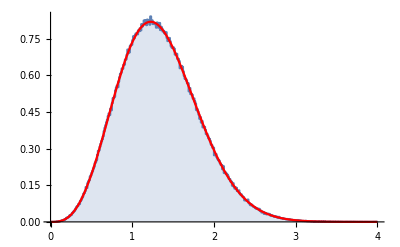

```mathematica
test$x3Gaussian[1000000]
```

```mathematica
x2Gaussian:=√(1/2(RandomVariate[NormalDistribution[0,1]])^2-Log[RandomReal[]]);
```

```mathematica
test$x2Gaussian[n_]:=Module[{h,d},
h=HistogramList[Table[x2Gaussian,n],{0,4,0.01},"PDF"];d=Transpose[{Drop[h[[1]],-1],h[[2]]}];Show[ListStepPlot[d,Filling->Axis],Plot[4/(√π)x^2 Exp[-x^2],{x,0,4},PlotStyle->Red]]]
```

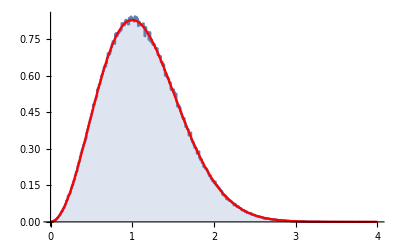

```mathematica
test$x2Gaussian[1000000]
```

```mathematica
getVpAndCosine[vpRms_,vn_]:=
Module[{β,y,x,μ,vp},
β=1/(√2 vpRms);
y=β vn;
While[True,
x=If[RandomReal[]<2/(√π y+2),x3Gaussian,x2Gaussian];
vp=x/β;
μ=RandomReal[{-1,1}];
If[RandomReal[]<(√(vn^2+vp^2-2vn vp μ))/(vn+vp),Break[]];
];
{vp,μ}
]
```

```mathematica
Timing[
vpPairs=
Reap[
With[{erg0=2.53 10^-8,reps=10000,vol=200^3,mn=939.565,mp=938.272,kT=2.53*^-8},
Module[{vn},
vn=√(2 erg0/mn);
For[i=0,i<reps,i++,
Sow[getVpAndCosine[√(kT/mp),vn]];
]
]
]
][[2,1]];
]
```

{0.639604,Null}

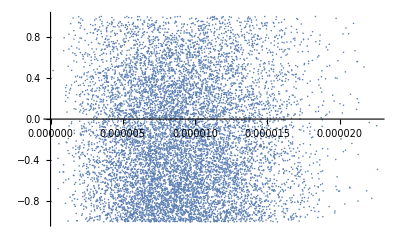

```mathematica
ListPlot[vpPairs]
```

```mathematica
Correlation[vpPairs]
```

{{1.,0.00880304},{0.00880304,1.}}

```mathematica
scatterE[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,vn,vp,μ,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
vecVn=vn{1,0,0};
vecVp=vp{μ,√(1-μ^2),0};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
1/2 mn vecVnout.vecVnout];
```

```mathematica
scatterEwithCosine[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,vn,vp,μ,sinmu,phi,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
vecVn=vn{1,0,0};
sinmu=√(1-μ^2);
phi=RandomReal[{0,2π}];
vecVp=vp{μ,sinmu Sin[phi],sinmu Cos[phi]};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
{1/2 mn vecVnout.vecVnout,vecVnout[[1]]/Norm[vecVnout]}];
```

```mathematica
scatterEwithCosineBadly[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,vn,vp,μ,sinmu,phi,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
vecVn=vn{1,0,0};
sinmu=√(1-μ^2);
phi=RandomReal[{0,2π}];
vecVp=vp{-μ,sinmu Sin[phi],sinmu Cos[phi]};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
{1/2 mn vecVnout.vecVnout,vecVnout[[1]]/Norm[vecVnout]}];
```

```mathematica
scatterEB[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,dir,vn,vp,μ,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
dir = randomDirection;
vecVn=vn{1,0,0};
(* μ=RandomReal[{-1,1}]; *)
μ=0;
vecVp=vp{μ,√(1-μ^2),0};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]dir-vecVcm;
1/2 mn vecVnout.vecVnout];
```

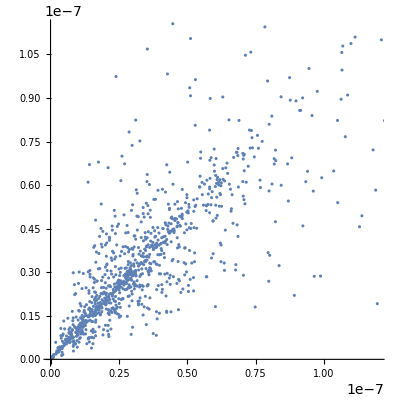

```mathematica
ListPlot[Table[scatterEB[2.53 10^-8],1000],AspectRatio->1]
```

```mathematica
Correlation[Table[scatterEB[2.53 10^-8],1000]]
```

{{1.,0.841879},{0.841879,1.}}

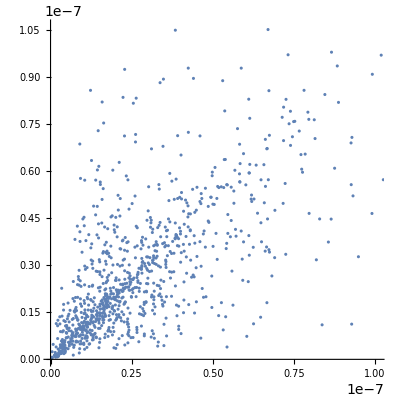

```mathematica
ListPlot[Table[scatterEB[1.0 10^-8],1000],AspectRatio->1]
```

```mathematica
Correlation[Table[scatterEB[1.00 10^-8],1000]]
```

{{1.,0.760737},{0.760737,1.}}

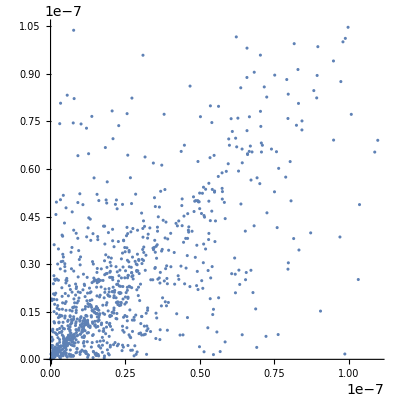

```mathematica
ListPlot[Table[scatterEB[0.1 10^-8],1000],AspectRatio->1]
```

```mathematica
realVals={mn->939.565,mp->938.272,kT->2.53*^-8};
```

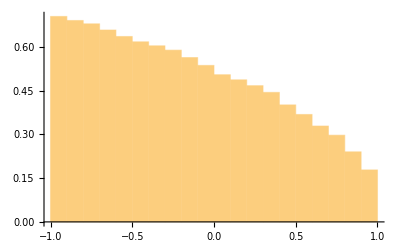

```mathematica
Histogram[Table[getVpAndCosine[√(kT/mp)/.realVals,√(2 kT/mn)/.realVals][[2]],100000],{-1,1,0.1},"PDF"]
```

```mathematica
Table[scatterE[2.53*^-8],10]
```

{7.14951×10^-8,6.61606×10^-8,1.30526×10^-8,1.58997×10^-8,3.52635×10^-8,7.02567×10^-8,5.98784×10^-9,4.73665×10^-8,4.8046×10^-8,2.2883×10^-8}

```mathematica
factor = 0.082572 0.025 csElasticH[2.53*^-8]/(4π 20.5^2)
```

0.0000117585

```mathematica
factor = (1-Exp[-0.082572 0.025 csElasticH[2.53*^-8]])/(4π 20.5^2)
```

0.0000114008

```mathematica
Timing[hlist2=HistogramList[Table[scatterE[2.53*^-8],10000000],{1.0*^-9}];]
```

{1299.25,Null}

```mathematica
?plotData
```

```mathematica
distForExport[hl_,f_]:=Transpose[{10^6 Drop[hl[[1]],-1],f/Total[hl[[2]]]Insert[Drop[hl[[2]],-1],0,1]}]
```

```mathematica
Export["c:\\git\\fusor-stuff\\mcnp\\cwEnergyScatter0D.csv",distForExport[hlist2,factor],"CSV"]
```

c:\git\fusor-stuff\mcnp\cwEnergyScatter0D.csv

```mathematica
hlist2
```

{{0.,1.×10^-9,2.×10^-9,3.×10^-9,4.×10^-9,5.×10^-9,6.×10^-9,7.×10^-9,8.×10^-9,9.×10^-9,1.×10^-8,1.1×10^-8,1.2×10^-8,1.3×10^-8,1.4×10^-8,1.5×10^-8,1.6×10^-8,1.7×10^-8,1.8×10^-8,1.9×10^-8,2.×10^-8,2.1×10^-8,2.2×10^-8,2.3×10^-8,2.4×10^-8,2.5×10^-8,2.6×10^-8,2.7×10^-8,2.8×10^-8,2.9×10^-8,3.×10^-8,3.1×10^-8,3.2×10^-8,3.3×10^-8,3.4×10^-8,3.5×10^-8,3.6×10^-8,3.7×10^-8,3.8×10^-8,3.9×10^-8,4.×10^-8,4.1×10^-8,4.2×10^-8,4.3×10^-8,4.4×10^-8,4.5×10^-8,4.6×10^-8,4.7×10^-8,4.8×10^-8,4.9×10^-8,5.×10^-8,5.1×10^-8,5.2×10^-8,5.3×10^-8,5.4×10^-8,5.5×10^-8,5.6×10^-8,5.7×10^-8,5.8×10^-8,5.9×10^-8,6.×10^-8,6.1×10^-8,6.2×10^-8,6.3×10^-8,6.4×10^-8,6.5×10^-8,6.6×10^-8,6.7×10^-8,6.8×10^-8,6.9×10^-8,7.×10^-8,7.1×10^-8,7.2×10^-8,7.3×10^-8,7.4×10^-8,7.5×10^-8,7.6×10^-8,7.7×10^-8,7.8×10^-8,7.9×10^-8,8.×10^-8,8.1×10^-8,8.2×10^-8,8.3×10^-8,8.4×10^-8,8.5×10^-8,8.6×10^-8,8.7×10^-8,8.8×10^-8,8.9×10^-8,9.×10^-8,9.1×10^-8,9.2×10^-8,9.3×10^-8,9.4×10^-8,9.5×10^-8,9.6×10^-8,9.7×10^-8,9.8×10^-8,9.9×10^-8,1.×10^-7,1.01×10^-7,1.02×10^-7,1.03×10^-7,1.04×10^-7,1.05×10^-7,1.06×10^-7,1.07×10^-7,1.08×10^-7,1.09×10^-7,1.1×10^-7,1.11×10^-7,1.12×10^-7,1.13×10^-7,1.14×10^-7,1.15×10^-7,1.16×10^-7,1.17×10^-7,1.18×10^-7,1.19×10^-7,1.2×10^-7,1.21×10^-7,1.22×10^-7,1.23×10^-7,1.24×10^-7,1.25×10^-7,1.26×10^-7,1.27×10^-7,1.28×10^-7,1.29×10^-7,1.3×10^-7,1.31×10^-7,1.32×10^-7,1.33×10^-7,1.34×10^-7,1.35×10^-7,1.36×10^-7,1.37×10^-7,1.38×10^-7,1.39×10^-7,1.4×10^-7,1.41×10^-7,1.42×10^-7,1.43×10^-7,1.44×10^-7,1.45×10^-7,1.46×10^-7,1.47×10^-7,1.48×10^-7,1.49×10^-7,1.5×10^-7,1.51×10^-7,1.52×10^-7,1.53×10^-7,1.54×10^-7,1.55×10^-7,1.56×10^-7,1.57×10^-7,1.58×10^-7,1.59×10^-7,1.6×10^-7,1.61×10^-7,1.62×10^-7,1.63×10^-7,1.64×10^-7,1.65×10^-7,1.66×10^-7,1.67×10^-7,1.68×10^-7,1.69×10^-7,1.7×10^-7,1.71×10^-7,1.72×10^-7,1.73×10^-7,1.74×10^-7,1.75×10^-7,1.76×10^-7,1.77×10^-7,1.78×10^-7,1.79×10^-7,1.8×10^-7,1.81×10^-7,1.82×10^-7,1.83×10^-7,1.84×10^-7,1.85×10^-7,1.86×10^-7,1.87×10^-7,1.88×10^-7,1.89×10^-7,1.9×10^-7,1.91×10^-7,1.92×10^-7,1.93×10^-7,1.94×10^-7,1.95×10^-7,1.96×10^-7,1.97×10^-7,1.98×10^-7,1.99×10^-7,2.×10^-7,2.01×10^-7,2.02×10^-7,2.03×10^-7,2.04×10^-7,2.05×10^-7,2.06×10^-7,2.07×10^-7,2.08×10^-7,2.09×10^-7,2.1×10^-7,2.11×10^-7,2.12×10^-7,2.13×10^-7,2.14×10^-7,2.15×10^-7,2.16×10^-7,2.17×10^-7,2.18×10^-7,2.19×10^-7,2.2×10^-7,2.21×10^-7,2.22×10^-7,2.23×10^-7,2.24×10^-7,2.25×10^-7,2.26×10^-7,2.27×10^-7,2.28×10^-7,2.29×10^-7,2.3×10^-7,2.31×10^-7,2.32×10^-7,2.33×10^-7,2.34×10^-7,2.35×10^-7,2.36×10^-7,2.37×10^-7,2.38×10^-7,2.39×10^-7,2.4×10^-7,2.41×10^-7,2.42×10^-7,2.43×10^-7,2.44×10^-7,2.45×10^-7,2.46×10^-7,2.47×10^-7,2.48×10^-7,2.49×10^-7,2.5×10^-7,2.51×10^-7,2.52×10^-7,2.53×10^-7,2.54×10^-7,2.55×10^-7,2.56×10^-7,2.57×10^-7,2.58×10^-7,2.59×10^-7,2.6×10^-7,2.61×10^-7,2.62×10^-7,2.63×10^-7,2.64×10^-7,2.65×10^-7,2.66×10^-7,2.67×10^-7,2.68×10^-7,2.69×10^-7,2.7×10^-7,2.71×10^-7,2.72×10^-7,2.73×10^-7,2.74×10^-7,2.75×10^-7,2.76×10^-7,2.77×10^-7,2.78×10^-7,2.79×10^-7,2.8×10^-7,2.81×10^-7,2.82×10^-7,2.83×10^-7,2.84×10^-7,2.85×10^-7,2.86×10^-7,2.87×10^-7,2.88×10^-7,2.89×10^-7,2.9×10^-7,2.91×10^-7,2.92×10^-7,2.93×10^-7,2.94×10^-7,2.95×10^-7,2.96×10^-7,2.97×10^-7,2.98×10^-7,2.99×10^-7,3.×10^-7,3.01×10^-7,3.02×10^-7,3.03×10^-7,3.04×10^-7,3.05×10^-7,3.06×10^-7,3.07×10^-7,3.08×10^-7,3.09×10^-7,3.1×10^-7,3.11×10^-7,3.12×10^-7,3.13×10^-7,3.14×10^-7,3.15×10^-7,3.16×10^-7,3.17×10^-7,3.18×10^-7,3.19×10^-7,3.2×10^-7,3.21×10^-7,3.22×10^-7,3.23×10^-7,3.24×10^-7,3.25×10^-7,3.26×10^-7,3.27×10^-7,3.28×10^-7,3.29×10^-7,3.3×10^-7,3.31×10^-7,3.32×10^-7,3.33×10^-7,3.34×10^-7,3.35×10^-7,3.36×10^-7,3.37×10^-7,3.38×10^-7,3.39×10^-7,3.4×10^-7,3.41×10^-7,3.42×10^-7,3.43×10^-7,3.44×10^-7,3.45×10^-7,3.46×10^-7,3.47×10^-7,3.48×10^-7,3.49×10^-7,3.5×10^-7,3.51×10^-7,3.52×10^-7,3.53×10^-7,3.54×10^-7,3.55×10^-7,3.56×10^-7,3.57×10^-7,3.58×10^-7,3.59×10^-7,3.6×10^-7,3.61×10^-7,3.62×10^-7,3.63×10^-7,3.64×10^-7,3.65×10^-7,3.66×10^-7,3.67×10^-7,3.68×10^-7,3.69×10^-7,3.7×10^-7,3.71×10^-7,3.72×10^-7,3.73×10^-7,3.74×10^-7,3.75×10^-7,3.76×10^-7,3.77×10^-7,3.78×10^-7,3.79×10^-7,3.8×10^-7,3.81×10^-7,3.82×10^-7,3.83×10^-7,3.84×10^-7,3.85×10^-7,3.86×10^-7,3.87×10^-7,3.88×10^-7,3.89×10^-7,3.9×10^-7,3.91×10^-7,3.92×10^-7,3.93×10^-7,3.94×10^-7,3.95×10^-7,3.96×10^-7,3.97×10^-7,3.98×10^-7,3.99×10^-7,4.×10^-7,4.01×10^-7,4.02×10^-7,4.03×10^-7,4.04×10^-7,4.05×10^-7,4.06×10^-7,4.07×10^-7,4.08×10^-7,4.09×10^-7,4.1×10^-7,4.11×10^-7,4.12×10^-7,4.13×10^-7,4.14×10^-7,4.15×10^-7,4.16×10^-7,4.17×10^-7,4.18×10^-7,4.19×10^-7,4.2×10^-7,4.21×10^-7,4.22×10^-7,4.23×10^-7,4.24×10^-7,4.25×10^-7,4.26×10^-7,4.27×10^-7,4.28×10^-7,4.29×10^-7,4.3×10^-7,4.31×10^-7,4.32×10^-7},{39741,71883,92580,107740,120180,132351,141753,150039,157567,164977,171217,176973,181825,187236,192099,196696,200327,204478,207069,210539,213547,216758,219570,222490,225285,223136,216295,207310,198480,192215,184423,177745,170920,164406,157298,151499,145183,139385,133914,129260,124348,119507,115183,110318,105118,102095,97502,94447,90791,87116,83557,80354,77355,74357,71350,68446,65897,63672,61030,58434,55934,53931,52171,49777,48250,46040,44388,42646,40841,39726,37938,36220,35170,33800,32730,31027,29913,28512,27522,26406,25588,24812,23700,22567,21754,20714,20126,19442,18531,17804,17501,16595,16009,15277,14712,14204,13385,13218,12596,11928,11682,11024,10750,10486,9844,9365,9085,8795,8486,8071,7848,7570,7145,6958,6596,6448,6206,6005,5578,5420,5260,5006,4872,4686,4399,4314,4189,3978,3921,3669,3481,3459,3278,3130,3010,2910,2796,2692,2535,2530,2394,2268,2274,2139,2037,1920,1936,1785,1721,1706,1599,1504,1474,1371,1376,1364,1300,1210,1181,1127,1122,1000,1046,961,944,911,851,825,803,746,770,726,681,633,582,589,587,577,528,518,485,453,480,459,439,462,369,367,383,333,358,313,311,271,308,253,249,248,256,238,250,187,202,202,179,174,169,173,168,141,143,132,152,136,116,106,121,112,125,115,101,104,107,89,74,86,73,63,61,71,67,78,63,55,79,68,57,43,43,52,40,55,39,34,34,46,28,22,29,42,29,33,33,32,35,32,26,25,17,20,18,21,22,19,20,15,10,15,12,14,16,17,10,15,12,7,15,12,9,5,8,14,8,5,10,8,4,12,6,9,3,7,4,12,4,3,4,7,12,4,4,3,5,1,3,3,4,5,3,6,1,3,2,3,4,0,2,3,2,3,1,3,2,2,2,1,3,0,1,2,2,1,3,0,4,0,0,1,0,2,2,1,0,0,0,2,2,0,3,0,1,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
data2=plotData[hlist2,factor];
```

```mathematica
data2
```

{{0.,4.5308×10^-8},{0.001,8.19525×10^-8},{0.002,1.05549×10^-7},{0.003,1.22832×10^-7},{0.004,1.37015×10^-7},{0.005,1.50891×10^-7},{0.006,1.6161×10^-7},{0.007,1.71057×10^-7},{0.008,1.79639×10^-7},{0.009,1.88087×10^-7},{0.01,1.95201×10^-7},{0.011,2.01764×10^-7},{0.012,2.07295×10^-7},{0.013,2.13464×10^-7},{0.014,2.19009×10^-7},{0.015,2.2425×10^-7},{0.016,2.28389×10^-7},{0.017,2.33122×10^-7},{0.018,2.36076×10^-7},{0.019,2.40032×10^-7},{0.02,2.43461×10^-7},{0.021,2.47122×10^-7},{0.022,2.50328×10^-7},{0.023,2.53657×10^-7},{0.024,2.56843×10^-7},{0.025,2.54393×10^-7},{0.026,2.46594×10^-7},{0.027,2.3635×10^-7},{0.028,2.26283×10^-7},{0.029,2.19141×10^-7},{0.03,2.10257×10^-7},{0.031,2.02644×10^-7},{0.032,1.94863×10^-7},{0.033,1.87436×10^-7},{0.034,1.79333×10^-7},{0.035,1.72721×10^-7},{0.036,1.65521×10^-7},{0.037,1.5891×10^-7},{0.038,1.52673×10^-7},{0.039,1.47367×10^-7},{0.04,1.41767×10^-7},{0.041,1.36248×10^-7},{0.042,1.31318×10^-7},{0.043,1.25772×10^-7},{0.044,1.19843×10^-7},{0.045,1.16397×10^-7},{0.046,1.1116×10^-7},{0.047,1.07677×10^-7},{0.048,1.03509×10^-7},{0.049,9.93194×10^-8},{0.05,9.52618×10^-8},{0.051,9.16101×10^-8},{0.052,8.8191×10^-8},{0.053,8.47731×10^-8},{0.054,8.13448×10^-8},{0.055,7.8034×10^-8},{0.056,7.5128×10^-8},{0.057,7.25913×10^-8},{0.058,6.95792×10^-8},{0.059,6.66195×10^-8},{0.06,6.37693×10^-8},{0.061,6.14858×10^-8},{0.062,5.94792×10^-8},{0.063,5.67499×10^-8},{0.064,5.5009×10^-8},{0.065,5.24894×10^-8},{0.066,5.0606×10^-8},{0.067,4.86199×10^-8},{0.068,4.65621×10^-8},{0.069,4.52909×10^-8},{0.07,4.32524×10^-8},{0.071,4.12938×10^-8},{0.072,4.00967×10^-8},{0.073,3.85348×10^-8},{0.074,3.73149×10^-8},{0.075,3.53733×10^-8},{0.076,3.41033×10^-8},{0.077,3.2506×10^-8},{0.078,3.13773×10^-8},{0.079,3.0105×10^-8},{0.08,2.91724×10^-8},{0.081,2.82877×10^-8},{0.082,2.70199×10^-8},{0.083,2.57282×10^-8},{0.084,2.48013×10^-8},{0.085,2.36157×10^-8},{0.086,2.29453×10^-8},{0.087,2.21655×10^-8},{0.088,2.11269×10^-8},{0.089,2.0298×10^-8},{0.09,1.99526×10^-8},{0.091,1.89197×10^-8},{0.092,1.82516×10^-8},{0.093,1.7417×10^-8},{0.094,1.67729×10^-8},{0.095,1.61937×10^-8},{0.096,1.526×10^-8},{0.097,1.50696×10^-8},{0.098,1.43605×10^-8},{0.099,1.35989×10^-8},{0.1,1.33184×10^-8},{0.101,1.25683×10^-8},{0.102,1.22559×10^-8},{0.103,1.19549×10^-8},{0.104,1.1223×10^-8},{0.105,1.06769×10^-8},{0.106,1.03576×10^-8},{0.107,1.0027×10^-8},{0.108,9.67473×10^-9},{0.109,9.2016×10^-9},{0.11,8.94736×10^-9},{0.111,8.63042×10^-9},{0.112,8.14589×10^-9},{0.113,7.93269×10^-9},{0.114,7.51998×10^-9},{0.115,7.35125×10^-9},{0.116,7.07535×10^-9},{0.117,6.84619×10^-9},{0.118,6.35938×10^-9},{0.119,6.17924×10^-9},{0.12,5.99683×10^-9},{0.121,5.70725×10^-9},{0.122,5.55448×10^-9},{0.123,5.34242×10^-9},{0.124,5.01522×10^-9},{0.125,4.91831×10^-9},{0.126,4.7758×10^-9},{0.127,4.53525×10^-9},{0.128,4.47026×10^-9},{0.129,4.18296×10^-9},{0.13,3.96863×10^-9},{0.131,3.94354×10^-9},{0.132,3.73719×10^-9},{0.133,3.56846×10^-9},{0.134,3.43165×10^-9},{0.135,3.31764×10^-9},{0.136,3.18767×10^-9},{0.137,3.0691×10^-9},{0.138,2.89011×10^-9},{0.139,2.88441×10^-9},{0.14,2.72936×10^-9},{0.141,2.58571×10^-9},{0.142,2.59255×10^-9},{0.143,2.43864×10^-9},{0.144,2.32235×10^-9},{0.145,2.18896×10^-9},{0.146,2.2072×10^-9},{0.147,2.03505×10^-9},{0.148,1.96208×10^-9},{0.149,1.94498×10^-9},{0.15,1.82299×10^-9},{0.151,1.71468×10^-9},{0.152,1.68048×10^-9},{0.153,1.56305×10^-9},{0.154,1.56875×10^-9},{0.155,1.55507×10^-9},{0.156,1.48211×10^-9},{0.157,1.3795×10^-9},{0.158,1.34644×10^-9},{0.159,1.28487×10^-9},{0.16,1.27917×10^-9},{0.161,1.14008×10^-9},{0.162,1.19253×10^-9},{0.163,1.09562×10^-9},{0.164,1.07624×10^-9},{0.165,1.03861×10^-9},{0.166,9.7021×10^-10},{0.167,9.40568×10^-10},{0.168,9.15486×10^-10},{0.169,8.50501×10^-10},{0.17,8.77863×10^-10},{0.171,8.27699×10^-10},{0.172,7.76396×10^-10},{0.173,7.21672×10^-10},{0.174,6.63528×10^-10},{0.175,6.71508×10^-10},{0.176,6.69228×10^-10},{0.177,6.57827×10^-10},{0.178,6.01963×10^-10},{0.179,5.90562×10^-10},{0.18,5.5294×10^-10},{0.181,5.16457×10^-10},{0.182,5.47239×10^-10},{0.183,5.23298×10^-10},{0.184,5.00496×10^-10},{0.185,5.26718×10^-10},{0.186,4.2069×10^-10},{0.187,4.1841×10^-10},{0.188,4.36651×10^-10},{0.189,3.79647×10^-10},{0.19,4.08149×10^-10},{0.191,3.56846×10^-10},{0.192,3.54565×10^-10},{0.193,3.08962×10^-10},{0.194,3.51145×10^-10},{0.195,2.88441×10^-10},{0.196,2.8388×10^-10},{0.197,2.8274×10^-10},{0.198,2.91861×10^-10},{0.199,2.71339×10^-10},{0.2,2.8502×10^-10},{0.201,2.13195×10^-10},{0.202,2.30297×10^-10},{0.203,2.30297×10^-10},{0.204,2.04075×10^-10},{0.205,1.98374×10^-10},{0.206,1.92674×10^-10},{0.207,1.97234×10^-10},{0.208,1.91534×10^-10},{0.209,1.60752×10^-10},{0.21,1.63032×10^-10},{0.211,1.50491×10^-10},{0.212,1.73292×10^-10},{0.213,1.55051×10^-10},{0.214,1.32249×10^-10},{0.215,1.20849×10^-10},{0.216,1.3795×10^-10},{0.217,1.27689×10^-10},{0.218,1.4251×10^-10},{0.219,1.31109×10^-10},{0.22,1.15148×10^-10},{0.221,1.18569×10^-10},{0.222,1.21989×10^-10},{0.223,1.01467×10^-10},{0.224,8.43661×10^-11},{0.225,9.8047×10^-11},{0.226,8.3226×10^-11},{0.227,7.18252×10^-11},{0.228,6.9545×10^-11},{0.229,8.09458×10^-11},{0.23,7.63855×10^-11},{0.231,8.89264×10^-11},{0.232,7.18252×10^-11},{0.233,6.27045×10^-11},{0.234,9.00665×10^-11},{0.235,7.75256×10^-11},{0.236,6.49847×10^-11},{0.237,4.90235×10^-11},{0.238,4.90235×10^-11},{0.239,5.92843×10^-11},{0.24,4.56033×10^-11},{0.241,6.27045×10^-11},{0.242,4.44632×10^-11},{0.243,3.87628×10^-11},{0.244,3.87628×10^-11},{0.245,5.24438×10^-11},{0.246,3.19223×10^-11},{0.247,2.50818×10^-11},{0.248,3.30624×10^-11},{0.249,4.78834×10^-11},{0.25,3.30624×10^-11},{0.251,3.76227×10^-11},{0.252,3.76227×10^-11},{0.253,3.64826×10^-11},{0.254,3.99029×10^-11},{0.255,3.64826×10^-11},{0.256,2.96421×10^-11},{0.257,2.8502×10^-11},{0.258,1.93814×10^-11},{0.259,2.28016×10^-11},{0.26,2.05215×10^-11},{0.261,2.39417×10^-11},{0.262,2.50818×10^-11},{0.263,2.16616×10^-11},{0.264,2.28016×10^-11},{0.265,1.71012×10^-11},{0.266,1.14008×10^-11},{0.267,1.71012×10^-11},{0.268,1.3681×10^-11},{0.269,1.59611×10^-11},{0.27,1.82413×10^-11},{0.271,1.93814×10^-11},{0.272,1.14008×10^-11},{0.273,1.71012×10^-11},{0.274,1.3681×10^-11},{0.275,7.98057×10^-12},{0.276,1.71012×10^-11},{0.277,1.3681×10^-11},{0.278,1.02607×10^-11},{0.279,5.70041×10^-12},{0.28,9.12066×10^-12},{0.281,1.59611×10^-11},{0.282,9.12066×10^-12},{0.283,5.70041×10^-12},{0.284,1.14008×10^-11},{0.285,9.12066×10^-12},{0.286,4.56033×10^-12},{0.287,1.3681×10^-11},{0.288,6.84049×10^-12},{0.289,1.02607×10^-11},{0.29,3.42025×10^-12},{0.291,7.98057×10^-12},{0.292,4.56033×10^-12},{0.293,1.3681×10^-11},{0.294,4.56033×10^-12},{0.295,3.42025×10^-12},{0.296,4.56033×10^-12},{0.297,7.98057×10^-12},{0.298,1.3681×10^-11},{0.299,4.56033×10^-12},{0.3,4.56033×10^-12},{0.301,3.42025×10^-12},{0.302,5.70041×10^-12},{0.303,1.14008×10^-12},{0.304,3.42025×10^-12},{0.305,3.42025×10^-12},{0.306,4.56033×10^-12},{0.307,5.70041×10^-12},{0.308,3.42025×10^-12},{0.309,6.84049×10^-12},{0.31,1.14008×10^-12},{0.311,3.42025×10^-12},{0.312,2.28016×10^-12},{0.313,3.42025×10^-12},{0.314,4.56033×10^-12},{0.315,0.},{0.316,2.28016×10^-12},{0.317,3.42025×10^-12},{0.318,2.28016×10^-12},{0.319,3.42025×10^-12},{0.32,1.14008×10^-12},{0.321,3.42025×10^-12},{0.322,2.28016×10^-12},{0.323,2.28016×10^-12},{0.324,2.28016×10^-12},{0.325,1.14008×10^-12},{0.326,3.42025×10^-12},{0.327,0.},{0.328,1.14008×10^-12},{0.329,2.28016×10^-12},{0.33,2.28016×10^-12},{0.331,1.14008×10^-12},{0.332,3.42025×10^-12},{0.333,0.},{0.334,4.56033×10^-12},{0.335,0.},{0.336,0.},{0.337,1.14008×10^-12},{0.338,0.},{0.339,2.28016×10^-12},{0.34,2.28016×10^-12},{0.341,1.14008×10^-12},{0.342,0.},{0.343,0.},{0.344,0.},{0.345,2.28016×10^-12},{0.346,2.28016×10^-12},{0.347,0.},{0.348,3.42025×10^-12},{0.349,0.},{0.35,1.14008×10^-12},{0.351,1.14008×10^-12},{0.352,0.},{0.353,1.14008×10^-12},{0.354,0.},{0.355,0.},{0.356,0.},{0.357,0.},{0.358,0.},{0.359,0.},{0.36,0.},{0.361,0.},{0.362,1.14008×10^-12},{0.363,1.14008×10^-12},{0.364,0.},{0.365,0.},{0.366,0.},{0.367,1.14008×10^-12},{0.368,1.14008×10^-12},{0.369,0.},{0.37,0.},{0.371,0.},{0.372,0.},{0.373,0.},{0.374,0.},{0.375,0.},{0.376,0.},{0.377,0.},{0.378,1.14008×10^-12},{0.379,0.},{0.38,0.},{0.381,0.},{0.382,1.14008×10^-12},{0.383,0.},{0.384,0.},{0.385,1.14008×10^-12},{0.386,0.},{0.387,1.14008×10^-12},{0.388,0.},{0.389,0.},{0.39,0.},{0.391,0.},{0.392,0.},{0.393,0.},{0.394,0.},{0.395,0.},{0.396,0.},{0.397,0.},{0.398,1.14008×10^-12},{0.399,0.},{0.4,0.},{0.401,0.},{0.402,1.14008×10^-12},{0.403,0.},{0.404,0.},{0.405,0.},{0.406,0.},{0.407,0.},{0.408,0.},{0.409,0.},{0.41,0.},{0.411,0.},{0.412,0.},{0.413,0.},{0.414,0.},{0.415,0.},{0.416,0.},{0.417,1.14008×10^-12},{0.418,0.},{0.419,0.},{0.42,0.},{0.421,0.},{0.422,0.},{0.423,0.},{0.424,0.},{0.425,0.},{0.426,0.},{0.427,0.},{0.428,0.},{0.429,0.},{0.43,0.},{0.431,1.14008×10^-12}}

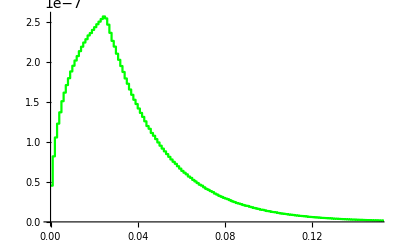

```mathematica
plot2=ListStepPlot[data2,PlotRange->{{0,0.15},All},PlotStyle->Green]
```

```mathematica
plotData[hlist_,f_]:=Transpose[{10^6 Drop[hlist[[1]],-1],f hlist[[2]]/Total[hlist[[2]]]}];
```

```mathematica
data1=plotData[hlist1,factor];
```

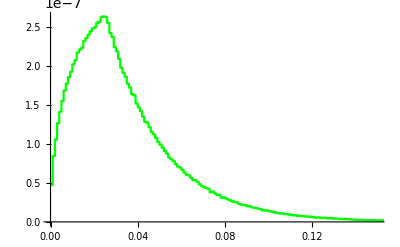

```mathematica
plot1=ListStepPlot[data1,PlotRange->{{0,0.15},All},PlotStyle->Green]
```

```mathematica
myLinearHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},AxesLabel->{"eV","(n/\!\(\*SuperscriptBox[\(cm\), \(2\)]\))/src"},Filling->Axis,PlotLabel->title<>"\nTotal = "<>ToString[Total[nList],TraditionalForm]<>"(n/\!\(\*SuperscriptBox[\(cm\), \(2\)]\))/src"]]
```

```mathematica
xRange={0,0.15}; yRange={0,3*^-7};
```

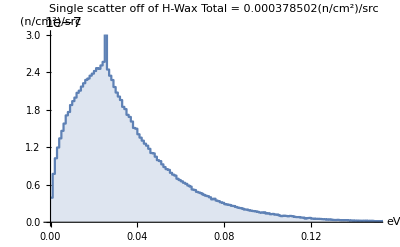

```mathematica
hist20124=myLinearHist[tally20124,"Single scatter off of H-Wax"]
```

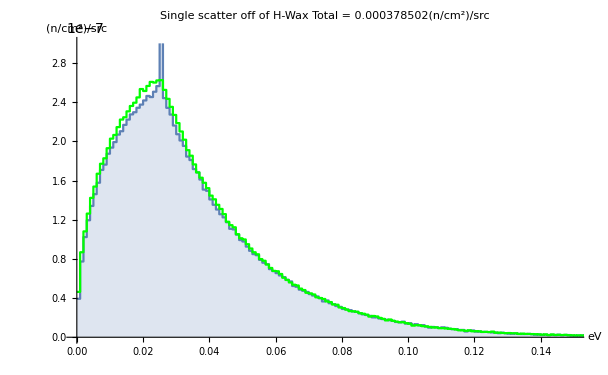

```mathematica
Show[hist20124,plot1]
```

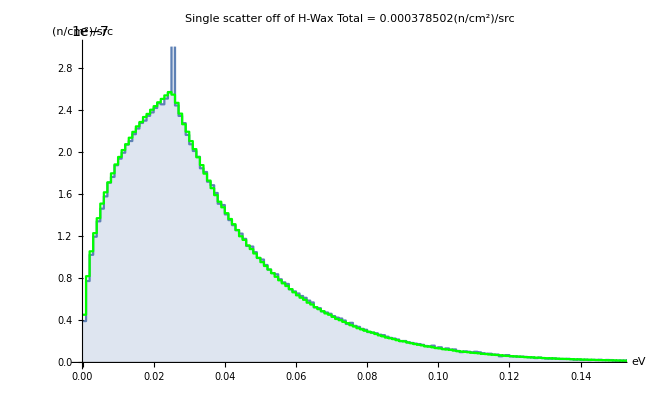

```mathematica
Show[hist20124,plot2]
```

```mathematica
getCsvTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"CSV"]];toPlot = Transpose[{Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
gm1=getCsvTallyFromClipboard[];
```

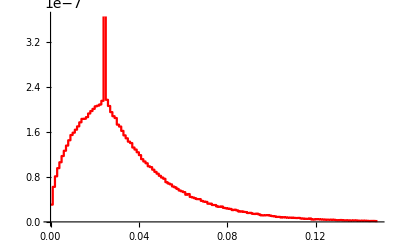

```mathematica
plotGm1=ListStepPlot[gm1[[4]],PlotStyle->Red]
```

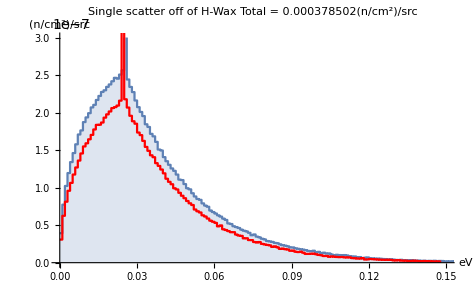

```mathematica
Show[hist20124,plotGm1]
```

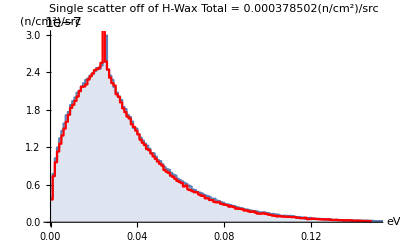

```mathematica
Show[hist20124,ListStepPlot[{#[[1]],1.18#[[2]]}&/@gm1[[4]],PlotStyle->Red]]
```

```mathematica
Timing[
ergPairs0D=
Reap[
With[{erg0=2.53 10^-8,reps=100000,vol=200^3},
Module[{pathLen,erg,erg1},
erg=erg0;
For[i=0,i<reps,i++,
erg1=scatterE[erg];
Sow[{erg,erg1}];
erg=erg1;
]
]
]
][[2,1]];
]
```

{13.0885,Null}

```mathematica
Correlation[ergPairs0D]
```

{{1.,0.468754},{0.468754,1.}}

```mathematica
Correlation[ergPairs0D]
```

{{1.,0.470281},{0.470281,1.}}

```mathematica
getTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"Table"]];toPlot = Transpose[{10^6 Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
myLinearHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},Filling->Axis,PlotLabel->title<>"
Total = "<>ToString[Total[nList],TraditionalForm]<>"(n/cm^2)/src"]]
```

```mathematica
tally2124=getTallyFromClipboard[];
```

```mathematica
xRange={0,0.15};yRange={0,5 10^-7};
```

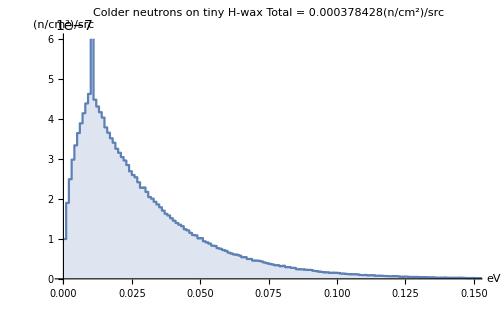

```mathematica
myLinearHist[tally2124,"Colder neutrons on tiny H-wax"]
```

```mathematica
Timing[hlist1$cold=HistogramList[Table[scatterE[1 10^-8],1000000],{1.0*^-9}];]
```

{134.317,Null}

```mathematica
factor$cold = (1-Exp[-0.082572 0.025 csElasticH[1 10^-8]])/(4π 20.5^2)
```

0.0000154906

```mathematica
data1$cold=plotData[hlist1$cold,factor$cold];
```

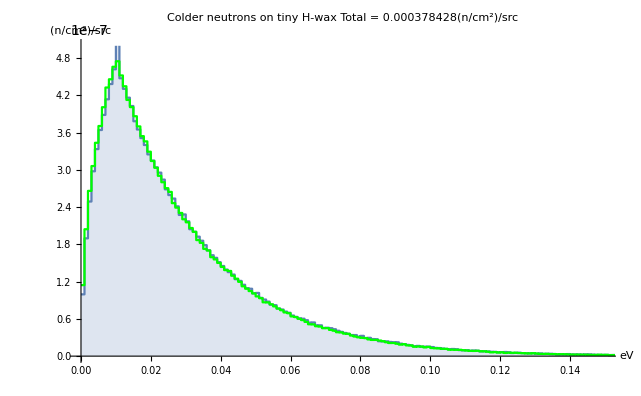

```mathematica
Show[myLinearHist[tally2124,"Colder neutrons on tiny H-wax"],ListStepPlot[data1$cold,PlotRange->{{0,0.15},All},PlotStyle->Green]]
```

```mathematica
Timing[hlist1$coldb=HistogramList[Table[scatterEB[1 10^-8],1000000],{1.0*^-9}];]
```

{146.937,Null}

```mathematica
data1$coldb=plotData[hlist1$coldb,factor$cold];
```

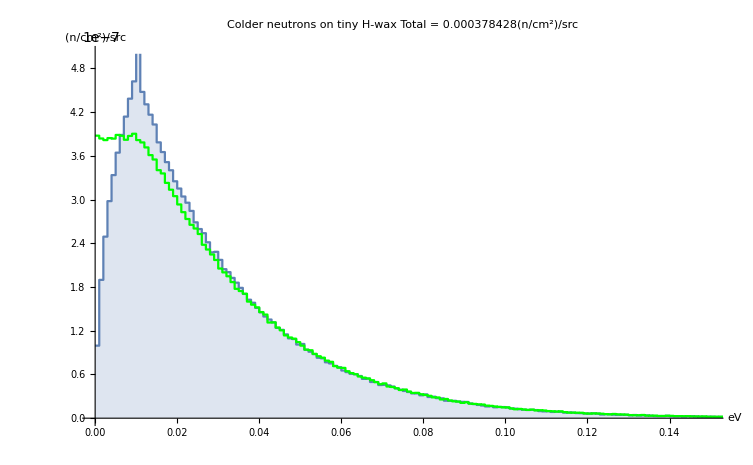

```mathematica
Show[myLinearHist[tally2124,"Colder neutrons on tiny H-wax"],ListStepPlot[data1$coldb,PlotRange->{{0,0.15},All},PlotStyle->Green]]
```

```mathematica
SetAttributes[newTally,HoldFirst];
newTally[t_,n_,bin_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Clear[t];t={Table[0,n],bin,0,0};];
SetAttributes[scoreTally,HoldFirst];
scoreTally[t_,x_,score_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{ibin},ibin=Ceiling[x/t[[BINSIZE]]];If[ibin>0 && ibin≤Length[t[[BINS]]],t[[BINS,ibin]]+=score];t[[SUMS]]+=score;t[[SUMSX]]+=score x;]];
SetAttributes[clearTally,HoldFirst];
clearTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{n=Length[t[[BINS]]],binsize=t[[BINSIZE]]},newTally[t,n,binsize]]];
listToPlotTally[t_,scale_:1]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{n=Length[t[[BINS]]],binsize=t[[BINSIZE]]},Table[{(i-1) binsize,scale t[[BINS,i]]},{i,1,n}]]];
meanTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},t[[SUMSX]]/t[[SUMS]]];
totalTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},t[[SUMS]]];
```

```mathematica
Timing[Module[{nParticles=10000,volume=200^3,erg0=2.53 10^-8,density=0.082572,
erg,pathLength,captured,σs,σa,Σtot},
newTally[tallyFlux,400,0.001];
newTally[tallyEnergy,400,0.001];
For[i=0, i<nParticles,i++,
erg=erg0;
captured=False;
While[!captured,
σs=csElasticH[erg];σa=csAbsH[erg];Σtot=density(σs+σa);
pathLength=-Log[RandomReal[]]/Σtot;
scoreTally[tallyFlux,10^6 erg,pathLength/volume/nParticles];
scoreTally[tallyEnergy,10^6 erg,1];
erg=scatterE[erg];
captured=RandomReal[]<σa/(σs+σa);
]
]
]]
```

{207.965,Null}

```mathematica
tallyEnergy
```

{{3991,7221,9351,10527,11666,12675,13323,13911,14392,14834,15086,15573,15633,15704,15971,15838,16051,15933,15796,15865,15777,15466,15702,15330,15145,25006,15129,14754,14711,14261,14033,13901,13734,13401,13204,12972,12549,12457,12316,11807,11879,11535,11411,11030,10861,10463,10218,10062,9939,9688,9281,9388,9060,8702,8700,8217,8031,7971,7752,7498,7313,7136,7129,6765,6621,6425,6302,6121,5861,5886,5608,5368,5219,5129,5020,4897,4827,4545,4498,4407,4223,3950,3986,3963,3657,3584,3443,3496,3364,3246,3200,3005,2918,2960,2934,2757,2652,2589,2501,2340,2373,2242,2226,2192,2101,1966,1923,1854,1751,1817,1801,1691,1644,1508,1494,1427,1349,1401,1324,1215,1294,1204,1246,1214,1151,1017,1035,1016,877,934,885,891,853,761,782,772,736,735,688,656,640,644,606,558,578,548,512,511,501,486,487,436,424,420,398,421,389,373,348,372,294,319,297,297,290,298,284,287,286,221,244,232,218,213,214,199,212,196,194,162,198,155,159,139,152,162,124,140,135,102,128,84,103,125,97,91,91,94,99,80,94,64,84,67,63,68,67,74,60,62,65,70,53,60,67,59,38,42,47,44,38,53,34,40,45,48,32,40,38,42,30,32,33,23,29,17,29,24,28,27,25,17,21,18,12,17,27,12,15,15,16,15,17,13,12,14,9,12,14,10,7,12,14,9,10,8,10,13,8,5,6,8,3,4,12,4,3,7,5,5,8,4,3,3,10,4,4,4,3,1,3,2,3,3,3,2,1,1,1,0,1,1,6,0,2,1,3,1,1,1,3,3,0,2,2,4,1,0,2,0,2,2,1,0,2,5,0,1,0,1,2,1,1,1,2,1,0,0,0,0,0,0,0,0,2,0,2,0,1,0,1,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0.001,1006169,44311.}

```mathematica
tallyFlux
```

{{3.76802×10^-9,1.11788×10^-8,1.86892×10^-8,2.39987×10^-8,2.99982×10^-8,3.58427×10^-8,4.05576×10^-8,4.47144×10^-8,4.94512×10^-8,5.18621×10^-8,5.55331×10^-8,6.01417×10^-8,6.12351×10^-8,6.38042×10^-8,6.65894×10^-8,6.67007×10^-8,7.01017×10^-8,7.05851×10^-8,7.07936×10^-8,7.23144×10^-8,7.35627×10^-8,7.303×10^-8,7.60657×10^-8,7.33641×10^-8,7.41517×10^-8,1.24421×10^-7,7.68093×10^-8,7.43363×10^-8,7.66044×10^-8,7.37822×10^-8,7.39747×10^-8,7.34634×10^-8,7.35748×10^-8,7.2296×10^-8,7.13801×10^-8,7.04477×10^-8,6.77289×10^-8,6.88462×10^-8,6.71426×10^-8,6.54484×10^-8,6.69081×10^-8,6.53895×10^-8,6.49927×10^-8,6.33522×10^-8,6.2904×10^-8,6.10903×10^-8,5.87481×10^-8,5.79248×10^-8,5.79739×10^-8,5.68683×10^-8,5.40227×10^-8,5.52666×10^-8,5.38711×10^-8,5.11597×10^-8,5.13185×10^-8,4.90674×10^-8,4.85666×10^-8,4.77952×10^-8,4.72151×10^-8,4.60354×10^-8,4.41307×10^-8,4.30611×10^-8,4.38562×10^-8,4.17476×10^-8,3.97451×10^-8,3.92073×10^-8,3.81528×10^-8,3.77337×10^-8,3.6768×10^-8,3.72097×10^-8,3.43584×10^-8,3.36986×10^-8,3.19986×10^-8,3.16602×10^-8,3.0979×10^-8,3.05353×10^-8,2.96843×10^-8,2.89437×10^-8,2.87626×10^-8,2.74516×10^-8,2.70412×10^-8,2.57982×10^-8,2.4597×10^-8,2.56862×10^-8,2.33677×10^-8,2.24826×10^-8,2.18188×10^-8,2.26676×10^-8,2.09746×10^-8,2.04551×10^-8,2.04357×10^-8,1.88394×10^-8,1.95715×10^-8,1.91281×10^-8,1.84256×10^-8,1.77×10^-8,1.75065×10^-8,1.68358×10^-8,1.60452×10^-8,1.52246×10^-8,1.5559×10^-8,1.42542×10^-8,1.437×10^-8,1.46757×10^-8,1.38002×10^-8,1.26895×10^-8,1.27868×10^-8,1.25676×10^-8,1.15338×10^-8,1.16137×10^-8,1.18268×10^-8,1.10556×10^-8,1.06231×10^-8,9.96761×10^-9,1.00246×10^-8,9.06587×10^-9,9.32624×10^-9,8.95412×10^-9,8.7754×10^-9,8.10943×10^-9,8.41052×10^-9,8.20053×10^-9,8.30133×10^-9,7.93729×10^-9,7.766×10^-9,7.37028×10^-9,7.11008×10^-9,6.97183×10^-9,6.03464×10^-9,6.19417×10^-9,6.01587×10^-9,6.00763×10^-9,5.98074×10^-9,5.13288×10^-9,5.58086×10^-9,5.19665×10^-9,4.73653×10^-9,5.30631×10^-9,4.3944×10^-9,4.34869×10^-9,4.1696×10^-9,4.34012×10^-9,4.02244×10^-9,3.79953×10^-9,4.01829×10^-9,3.67447×10^-9,3.19578×10^-9,3.62472×10^-9,3.61246×10^-9,3.13185×10^-9,3.1666×10^-9,2.80738×10^-9,2.75299×10^-9,3.1111×10^-9,2.63192×10^-9,2.88495×10^-9,2.46261×10^-9,2.73031×10^-9,2.51739×10^-9,2.85011×10^-9,2.13309×10^-9,2.23314×10^-9,1.87242×10^-9,2.02713×10^-9,2.06506×10^-9,1.89272×10^-9,1.84287×10^-9,1.83503×10^-9,1.91441×10^-9,1.51949×10^-9,1.45947×10^-9,1.76841×10^-9,1.52428×10^-9,1.52516×10^-9,1.31391×10^-9,1.27459×10^-9,1.19813×10^-9,1.34754×10^-9,1.27904×10^-9,1.1524×10^-9,1.20572×10^-9,9.98151×10^-10,9.71018×10^-10,1.03236×10^-9,1.10597×10^-9,1.19991×10^-9,8.87696×10^-10,9.78837×10^-10,9.23009×10^-10,7.74372×10^-10,9.67445×10^-10,5.74409×10^-10,7.24298×10^-10,8.27551×10^-10,6.92138×10^-10,6.28537×10^-10,5.55986×10^-10,5.46256×10^-10,6.55582×10^-10,5.70751×10^-10,6.31539×10^-10,4.65081×10^-10,5.87171×10^-10,3.35724×10^-10,3.18331×10^-10,4.65272×10^-10,4.8909×10^-10,5.73051×10^-10,3.49844×10^-10,3.70238×10^-10,4.62992×10^-10,4.96027×10^-10,3.80305×10^-10,4.29146×10^-10,4.50941×10^-10,4.35107×10^-10,2.94747×10^-10,3.07147×10^-10,2.99247×10^-10,2.99519×10^-10,2.81351×10^-10,3.90429×10^-10,2.45948×10^-10,2.45999×10^-10,3.5266×10^-10,2.74767×10^-10,2.05086×10^-10,3.35031×10^-10,2.10027×10^-10,2.61435×10^-10,2.40548×10^-10,2.2042×10^-10,2.32599×10^-10,1.41023×10^-10,1.8207×10^-10,1.34317×10^-10,2.20021×10^-10,1.66555×10^-10,2.1334×10^-10,1.46755×10^-10,1.68067×10^-10,1.26937×10^-10,1.18436×10^-10,1.25995×10^-10,7.71775×10^-11,1.15005×10^-10,1.59796×10^-10,5.7647×10^-11,6.70626×10^-11,8.62995×10^-11,1.06733×10^-10,1.37946×10^-10,1.27964×10^-10,5.96554×10^-11,4.40189×10^-11,9.61219×10^-11,8.85754×10^-11,9.94206×10^-11,7.95771×10^-11,4.27911×10^-11,1.69804×10^-11,6.34785×10^-11,8.613×10^-11,8.85743×10^-11,7.46992×10^-11,4.83214×10^-11,5.35005×10^-11,6.21808×10^-11,6.58822×10^-11,3.67352×10^-11,2.76729×10^-11,6.88244×10^-11,5.08466×10^-11,1.31207×10^-11,6.92071×10^-11,3.89482×10^-11,2.83209×10^-11,5.21795×10^-11,4.19017×10^-11,5.89112×10^-11,5.46632×10^-11,3.21555×10^-11,2.81509×10^-11,8.96892×10^-12,7.88526×10^-11,1.7317×10^-11,2.79874×10^-11,4.38493×10^-11,2.36775×10^-11,6.156×10^-12,2.93534×10^-11,1.99514×10^-11,8.54426×10^-12,3.53379×10^-11,1.21015×10^-11,8.27011×10^-12,8.08462×10^-12,1.52029×10^-12,1.29888×10^-11,0,6.14848×10^-12,3.86725×10^-12,3.08229×10^-11,0,1.31684×10^-11,5.61663×10^-12,2.07949×10^-11,5.30935×10^-12,8.946×10^-13,4.17373×10^-12,8.71348×10^-12,3.78099×10^-11,0,4.72467×10^-12,5.15399×10^-12,3.76453×10^-11,1.29928×10^-12,0,1.04538×10^-11,0,3.33635×10^-12,9.64148×10^-12,7.5114×10^-12,0,1.75763×10^-11,3.93969×10^-11,0,2.50149×10^-12,0,6.18078×10^-12,2.1824×10^-12,7.68323×10^-12,4.23622×10^-12,2.37949×10^-12,1.4122×10^-11,1.62622×10^-11,0,0,0,0,0,0,0,0,1.53755×10^-11,0,2.26678×10^-11,0,5.82513×10^-12,0,7.97566×10^-12,0,0,7.24816×10^-12,0,0,0,6.06049×10^-12,0,0,1.54791×10^-11,1.09577×10^-11,0,0,0,0,0,0,0,1.14153×10^-11,0,0,0,0,1.29196×10^-12,0,0,0,0,0,0,0,0,0,6.10502×10^-12,4.48282×10^-12,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0.001,5.20423×10^-6,2.6185×10^-7}

```mathematica
xRange={0,0.23};yRange=All;
```

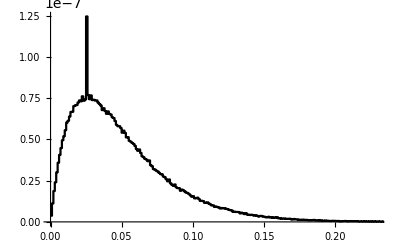

```mathematica
ListStepPlot[listToPlotTally[tallyFlux,1],PlotStyle->Black,PlotRange->{xRange,yRange}]
```

```mathematica
tallyNp0204=getTallyFromClipboard[];
```

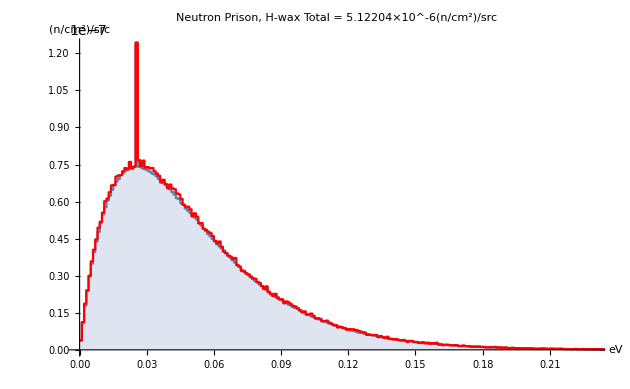

```mathematica
Show[myLinearHist[tallyNp0204,"Neutron Prison, H-wax"],ListStepPlot[listToPlotTally[tallyFlux,1],PlotStyle->Red,PlotRange->{xRange,yRange}]]
```

```mathematica
xRange={0,.23};yRange={0,1.4 10^-7};
```

```mathematica
gmPrison=getCsvTallyFromClipboard[];
```

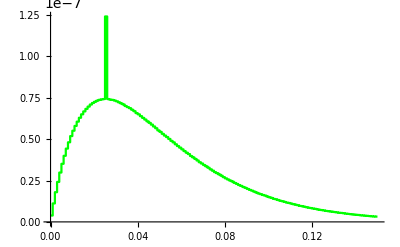

```mathematica
ListStepPlot[{#[[1]],#[[2]]/8}&/@gmPrison[[4]],PlotStyle->Green]
```

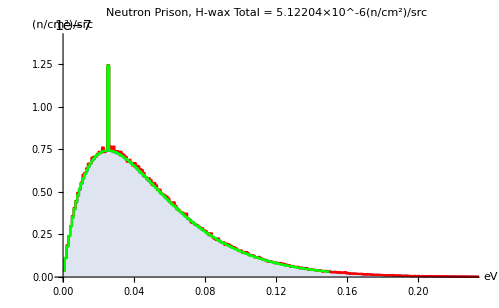

```mathematica
Show[myLinearHist[tallyNp0204,"Neutron Prison, H-wax"],ListStepPlot[listToPlotTally[tallyFlux,1],PlotStyle->Red,PlotRange->{xRange,yRange}],ListStepPlot[{#[[1]],#[[2]]/8}&/@gmPrison[[4]],PlotStyle->Green]]
```

```mathematica
gmPrisonFull=getCsvTallyFromClipboard[];
```

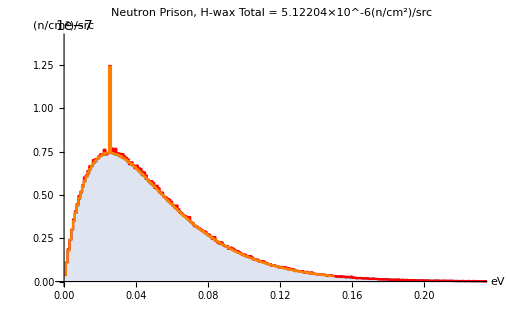

```mathematica
Show[myLinearHist[tallyNp0204,"Neutron Prison, H-wax"],ListStepPlot[listToPlotTally[tallyFlux,1],PlotStyle->Red,PlotRange->{xRange,yRange}],ListStepPlot[gmPrisonFull[[4]],PlotStyle->Orange]]
```

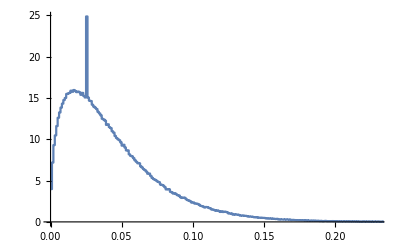

```mathematica
ListStepPlot[listToPlotTally[tallyEnergy,10^3/totalTally[tallyEnergy]],PlotRange->{xRange,yRange}]
```

```mathematica
tallyNp0214=getTallyFromClipboard[];
```

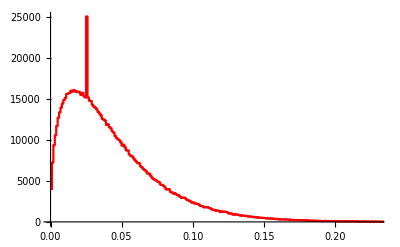

```mathematica
ListStepPlot[listToPlotTally[tallyEnergy,1],PlotStyle->Red,PlotRange->{xRange,yRange}]
```

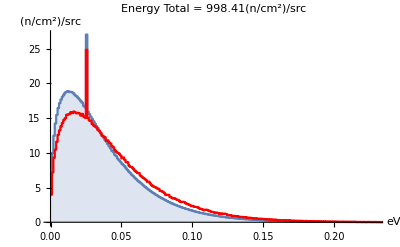

```mathematica
Show[myLinearHist[tallyNp0214,"Energy"],ListStepPlot[listToPlotTally[tallyEnergy,1000/totalTally[tallyEnergy]],PlotStyle->Red,PlotRange->{xRange,yRange}]]
```

```mathematica
tallyNp0414=getTallyFromClipboard[];
```

```mathematica
getDistFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList}=Transpose[ImportString[NotebookGet[ClipboardNotebook[]]⟦1,1,1⟧,"Table"]];toPlot=Transpose[{10^6 Drop[eList,-1],Drop[nList,1]/Total[nList]/(10^6(eList[[2]]-eList[[1]]))}];{eList,nList,errList,toPlot}]
```

```mathematica
distNp0414=getDistFromClipboard[];
```

```mathematica
{{myLinearDist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},AxesLabel->{"eV","dP/dE"},Filling->Axis,PlotLabel->title]];}}
```

{{Null}}

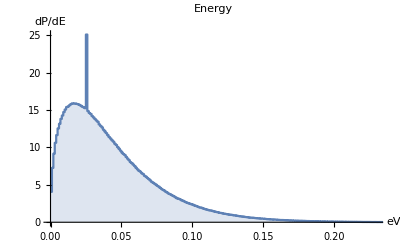

```mathematica
myLinearDist[distNp0414,"Energy"]
```

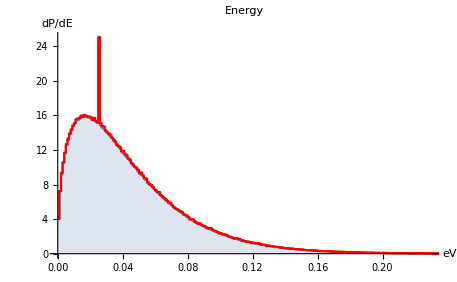

```mathematica
Show[myLinearDist[distNp0414,"Energy"],ListStepPlot[listToPlotTally[tallyEnergy,.001],PlotStyle->Red,PlotRange->{xRange,yRange}]]
```

```mathematica
gmTallyMaxwell=getCsvTallyFromClipboard[];
```

```mathematica
gmLinearHist[tally_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},Filling->Axis,PlotStyle->Red]]
```

```mathematica
gmLinearHist[tally_,color_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},PlotStyle->color]]
```

```mathematica
xRange={0,0.15}; yRange={0,3.5 10^-7};
```

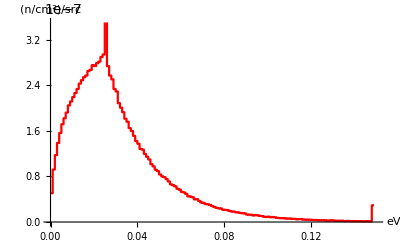

```mathematica
gmLinearHist[gmTallyMaxwell,Red]
```

```mathematica
gmTallyNewGmScatter=getCsvTallyFromClipboard[];
```

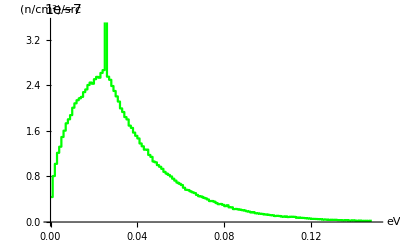

```mathematica
gmLinearHist[gmTallyNewGmScatter,Green]
```

```mathematica
gmTallyNewCwScatter=getCsvTallyFromClipboard[];
```

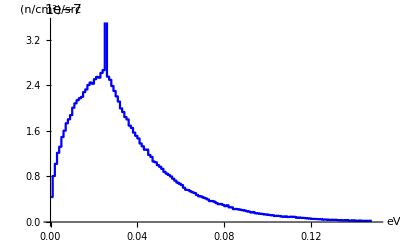

```mathematica
gmLinearHist[gmTallyNewGmScatter,Blue]
```

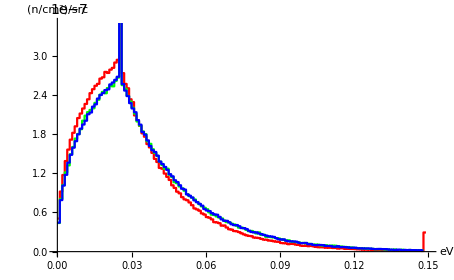

```mathematica
Show[gmLinearHist[gmTallyMaxwell,Red],gmLinearHist[gmTallyNewGmScatter,Green],gmLinearHist[gmTallyNewCwScatter,Blue]]
```

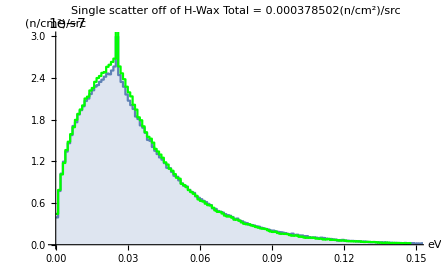

```mathematica
Show[hist20124,gmLinearHist[gmTallyNewCwScatter,Green]]
```

```mathematica
Export["c:\\git\\fusor-stuff\\mcnp\\tally20124.csv",Transpose[{10^6 tally20124[[1]],tally20124[[2]]}],"CSV"]
```

c:\git\fusor-stuff\mcnp\tally20124.csv

```mathematica
tally2201=getCosinesFromClipboard[];
```

```mathematica
getCosinesFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList}=Transpose[ImportString[NotebookGet[ClipboardNotebook[]]⟦1,1,1⟧,"Table"]];toPlot=Transpose[{Insert[eList,-1,1],Insert[nList,0,-1]/((Total[nList]-1) ((eList⟦2⟧-eList⟦1⟧)))}];{eList,nList,errList,toPlot}]
```

```mathematica
getCsvCosinesFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList}=Transpose[ImportString[NotebookGet[ClipboardNotebook[]]⟦1,1,1⟧,"CSV"]];
errList = {};
toPlot=Transpose[{Insert[eList,-1,1],Insert[nList,0,-1]/((Total[nList]-1) ((eList⟦2⟧-eList⟦1⟧)))}];{eList,nList,errList,toPlot}]
```

```mathematica
xRange={-1,1}; yRange={0,.001};
```

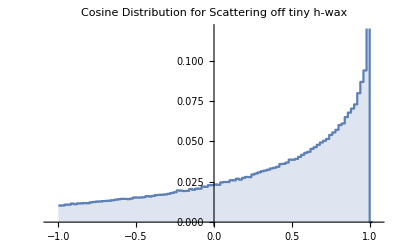

```mathematica
plot2201=ListStepPlot[tally2201[[4]],PlotRange->{{-1.05,1.05},{0,.12}},Filling->Axis,PlotLabel->"Cosine Distribution for Scattering off tiny h-wax"]
```

```mathematica
Total[tally2201[[2]]]
```

1.99931

```mathematica
Timing[hlistCos1=HistogramList[Table[scatterEwithCosine[2.53*^-8][[2]],1000000],{-1,1,0.02},"PDF"];]
```

{157.701,Null}

```mathematica
cosFactor = (1-Exp[-0.082572 0.025 csElasticH[2.53*^-8]])
```

0.0602079

```mathematica
Total[hlistCos1[[2]]]
```

50.

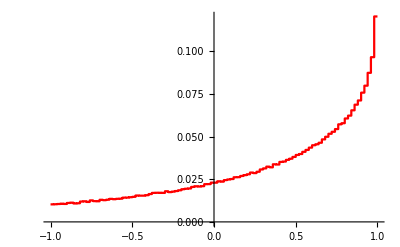

```mathematica
plotCosine0D=ListStepPlot[Transpose[{Drop[hlistCos1[[1]],-1],(cosFactor hlistCos1[[2]])/(Total[hlistCos1[[2]]]0.02)}],PlotStyle->Red]
```

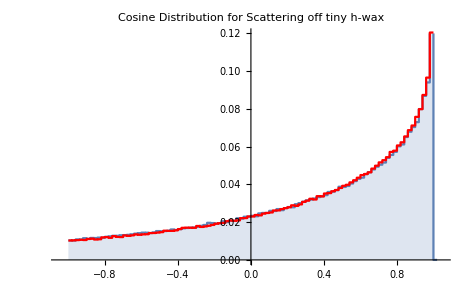

```mathematica
Show[plot2201,plotCosine0D]
```

```mathematica
gmCosines=getCsvCosinesFromClipboard[];
```

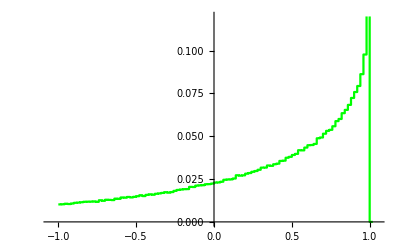

```mathematica
gmCosinesPlot=ListStepPlot[gmCosines[[4]],PlotRange->{{-1.05,1.05},{0,.12}},PlotStyle->Green]
```

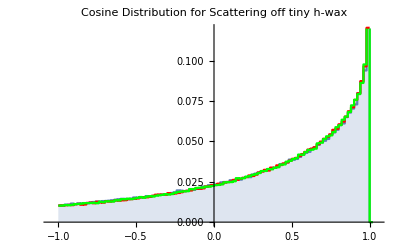

```mathematica
Show[plot2201,plotCosine0D,gmCosinesPlot]
```

```mathematica
csElasticH=Interpolation[ImportString["1.00000000e-11      1.16053e+03
1.03125000e-11      1.14282e+03
1.06250000e-11      1.12589e+03
1.09375000e-11      1.10969e+03
1.12500000e-11      1.09418e+03
1.15625000e-11      1.07930e+03
1.18750000e-11      1.06500e+03
1.21875000e-11      1.05127e+03
1.25000000e-11      1.03805e+03
1.28125000e-11      1.02531e+03
1.31250000e-11      1.01304e+03
1.34375000e-11      1.00119e+03
1.37500000e-11      9.89753e+02
1.43750000e-11      9.68006e+02
1.50000000e-11      9.47632e+02
1.56250000e-11      9.28494e+02
1.62500000e-11      9.10471e+02
1.68750000e-11      8.93458e+02
1.75000000e-11      8.77366e+02
1.81250000e-11      8.62113e+02
1.87500000e-11      8.47630e+02
1.93750000e-11      8.33853e+02
2.00000000e-11      8.20727e+02
2.09375000e-11      8.02152e+02
2.18750000e-11      7.84785e+02
2.28125000e-11      7.68499e+02
2.37500000e-11      7.53188e+02
2.46875000e-11      7.38758e+02
2.56250000e-11      7.25127e+02
2.65625000e-11      7.12224e+02
2.75000000e-11      6.99988e+02
2.84375000e-11      6.88361e+02
2.93750000e-11      6.77296e+02
3.03125000e-11      6.66748e+02
3.12500000e-11      6.56679e+02
3.21875000e-11      6.47053e+02
3.31250000e-11      6.37839e+02
3.40625000e-11      6.29007e+02
3.50000000e-11      6.20534e+02
3.59375000e-11      6.12394e+02
3.68750000e-11      6.04567e+02
3.78125000e-11      5.97032e+02
3.87500000e-11      5.89773e+02
3.96875000e-11      5.82773e+02
4.06250000e-11      5.76016e+02
4.25000000e-11      5.63181e+02
4.43750000e-11      5.51168e+02
4.62500000e-11      5.39893e+02
4.81250000e-11      5.29285e+02
5.00000000e-11      5.19278e+02
5.15625000e-11      5.11361e+02
5.31250000e-11      5.03795e+02
5.46875000e-11      4.96556e+02
5.62500000e-11      4.89621e+02
5.78125000e-11      4.82969e+02
5.93750000e-11      4.76581e+02
6.09375000e-11      4.70441e+02
6.25000000e-11      4.64533e+02
6.40625000e-11      4.58842e+02
6.56250000e-11      4.53356e+02
6.71875000e-11      4.48063e+02
6.87500000e-11      4.42951e+02
7.18750000e-11      4.33233e+02
7.50000000e-11      4.24128e+02
7.81250000e-11      4.15576e+02
8.12500000e-11      4.07523e+02
8.43750000e-11      3.99921e+02
8.75000000e-11      3.92731e+02
9.06250000e-11      3.85916e+02
9.37500000e-11      3.79445e+02
9.68750000e-11      3.73290e+02
1.00000000e-10      3.67426e+02
1.03125000e-10      3.61831e+02
1.06250000e-10      3.56485e+02
1.09375000e-10      3.51370e+02
1.12500000e-10      3.46470e+02
1.15625000e-10      3.41770e+02
1.18750000e-10      3.37257e+02
1.21875000e-10      3.32918e+02
1.25000000e-10      3.28744e+02
1.28125000e-10      3.24724e+02
1.31250000e-10      3.20848e+02
1.34375000e-10      3.17108e+02
1.37500000e-10      3.13497e+02
1.43750000e-10      3.06631e+02
1.50000000e-10      3.00199e+02
1.56250000e-10      2.94158e+02
1.62500000e-10      2.88470e+02
1.68750000e-10      2.83100e+02
1.75000000e-10      2.78022e+02
1.81250000e-10      2.73209e+02
1.87500000e-10      2.68639e+02
1.93750000e-10      2.64292e+02
2.00000000e-10      2.60151e+02
2.09375000e-10      2.54291e+02
2.18750000e-10      2.48813e+02
2.28125000e-10      2.43677e+02
2.37500000e-10      2.38848e+02
2.46875000e-10      2.34298e+02
2.56250000e-10      2.30000e+02
2.65625000e-10      2.25933e+02
2.75000000e-10      2.22076e+02
2.84375000e-10      2.18411e+02
2.93750000e-10      2.14924e+02
3.03125000e-10      2.11600e+02
3.12500000e-10      2.08428e+02
3.21875000e-10      2.05395e+02
3.31250000e-10      2.02492e+02
3.40625000e-10      1.99711e+02
3.50000000e-10      1.97042e+02
3.59375000e-10      1.94479e+02
3.68750000e-10      1.92014e+02
3.78125000e-10      1.89642e+02
3.87500000e-10      1.87357e+02
3.96875000e-10      1.85154e+02
4.06250000e-10      1.83027e+02
4.25000000e-10      1.78988e+02
4.43750000e-10      1.75209e+02
4.62500000e-10      1.71662e+02
4.81250000e-10      1.68326e+02
5.00000000e-10      1.65180e+02
5.15625000e-10      1.62691e+02
5.31250000e-10      1.60314e+02
5.46875000e-10      1.58039e+02
5.62500000e-10      1.55860e+02
5.78125000e-10      1.53771e+02
5.93750000e-10      1.51765e+02
6.09375000e-10      1.49837e+02
6.25000000e-10      1.47982e+02
6.40625000e-10      1.46196e+02
6.56250000e-10      1.44474e+02
6.71875000e-10      1.42814e+02
6.87500000e-10      1.41210e+02
7.18750000e-10      1.38162e+02
7.50000000e-10      1.35308e+02
7.81250000e-10      1.32628e+02
8.12500000e-10      1.30105e+02
8.43750000e-10      1.27724e+02
8.75000000e-10      1.25474e+02
9.06250000e-10      1.23341e+02
9.37500000e-10      1.21317e+02
9.68750000e-10      1.19392e+02
1.00000000e-09      1.17559e+02
1.03125000e-09      1.15811e+02
1.06250000e-09      1.14141e+02
1.09375000e-09      1.12544e+02
1.12500000e-09      1.11015e+02
1.15625000e-09      1.09548e+02
1.18750000e-09      1.08140e+02
1.21875000e-09      1.06788e+02
1.25000000e-09      1.05487e+02
1.28125000e-09      1.04234e+02
1.31250000e-09      1.03027e+02
1.34375000e-09      1.01863e+02
1.37500000e-09      1.00739e+02
1.43750000e-09      9.86033e+01
1.50000000e-09      9.66042e+01
1.56250000e-09      9.47279e+01
1.62500000e-09      9.29623e+01
1.68750000e-09      9.12971e+01
1.75000000e-09      8.97232e+01
1.81250000e-09      8.82326e+01
1.87500000e-09      8.68183e+01
1.93750000e-09      8.54741e+01
2.00000000e-09      8.41944e+01
2.09375000e-09      8.23853e+01
2.18750000e-09      8.06958e+01
2.28125000e-09      7.91134e+01
2.37500000e-09      7.76275e+01
2.46875000e-09      7.62287e+01
2.56250000e-09      7.49090e+01
2.65625000e-09      7.36613e+01
2.75000000e-09      7.24794e+01
2.84375000e-09      7.13578e+01
2.93750000e-09      7.02915e+01
3.03125000e-09      6.92764e+01
3.12500000e-09      6.83084e+01
3.21875000e-09      6.73841e+01
3.31250000e-09      6.65005e+01
3.40625000e-09      6.56545e+01
3.50000000e-09      6.48438e+01
3.59375000e-09      6.40659e+01
3.68750000e-09      6.33187e+01
3.78125000e-09      6.26004e+01
3.87500000e-09      6.19091e+01
3.96875000e-09      6.12433e+01
4.06250000e-09      6.06014e+01
4.25000000e-09      5.93840e+01
4.43750000e-09      5.82473e+01
4.62500000e-09      5.71830e+01
4.81250000e-09      5.61839e+01
5.00000000e-09      5.52437e+01
5.15625000e-09      5.45013e+01
5.31250000e-09      5.37933e+01
5.46875000e-09      5.31171e+01
5.62500000e-09      5.24706e+01
5.78125000e-09      5.18517e+01
5.93750000e-09      5.12585e+01
6.09375000e-09      5.06894e+01
6.25000000e-09      5.01428e+01
6.40625000e-09      4.96174e+01
6.56250000e-09      4.91118e+01
6.71875000e-09      4.86249e+01
6.87500000e-09      4.81555e+01
7.18750000e-09      4.72658e+01
7.50000000e-09      4.64354e+01
7.81250000e-09      4.56583e+01
8.12500000e-09      4.49292e+01
8.43750000e-09      4.42436e+01
8.75000000e-09      4.35976e+01
9.06250000e-09      4.29875e+01
9.37500000e-09      4.24103e+01
9.68750000e-09      4.18634e+01
1.00000000e-08      4.13442e+01
1.03125000e-08      4.08506e+01
1.06250000e-08      4.03807e+01
1.09375000e-08      3.99328e+01
1.12500000e-08      3.95052e+01
1.15625000e-08      3.90965e+01
1.18750000e-08      3.87055e+01
1.21875000e-08      3.83310e+01
1.25000000e-08      3.79720e+01
1.28125000e-08      3.76274e+01
1.31250000e-08      3.72964e+01
1.34375000e-08      3.69781e+01
1.37500000e-08      3.66718e+01
1.43750000e-08      3.60926e+01
1.50000000e-08      3.55538e+01
1.56250000e-08      3.50512e+01
1.62500000e-08      3.45811e+01
1.68750000e-08      3.41405e+01
1.75000000e-08      3.37265e+01
1.81250000e-08      3.33368e+01
1.87500000e-08      3.29693e+01
1.93750000e-08      3.26220e+01
2.00000000e-08      3.22933e+01
2.06625000e-08      3.19636e+01
2.13250000e-08      3.16516e+01
2.19875000e-08      3.13558e+01
2.26500000e-08      3.10751e+01
2.33125000e-08      3.08082e+01
2.39750000e-08      3.05542e+01
2.46375000e-08      3.03122e+01
2.53000000e-08      3.00812e+01
2.64578200e-08      2.97021e+01
2.76156300e-08      2.93512e+01
2.87734400e-08      2.90253e+01
2.99312500e-08      2.87220e+01
3.10890700e-08      2.84389e+01
3.22468800e-08      2.81741e+01
3.34046900e-08      2.79258e+01
3.45625000e-08      2.76927e+01
3.55273500e-08      2.75089e+01
3.64921900e-08      2.73340e+01
3.74570400e-08      2.71674e+01
3.84218800e-08      2.70084e+01
3.93867300e-08      2.68566e+01
4.03515700e-08      2.67114e+01
4.13164100e-08      2.65725e+01
4.22812500e-08      2.64395e+01
4.42109400e-08      2.61897e+01
4.61406300e-08      2.59594e+01
4.80703200e-08      2.57464e+01
5.00000000e-08      2.55489e+01
5.15625000e-08      2.53991e+01
5.31250000e-08      2.52578e+01
5.46875000e-08      2.51240e+01
5.62500000e-08      2.49974e+01
5.78125000e-08      2.48773e+01
5.93750000e-08      2.47632e+01
6.09375000e-08      2.46547e+01
6.25000000e-08      2.45515e+01
6.40625000e-08      2.44531e+01
6.56250000e-08      2.43592e+01
6.71875000e-08      2.42695e+01
6.87500000e-08      2.41838e+01
7.18750000e-08      2.40232e+01
7.50000000e-08      2.38756e+01
7.81250000e-08      2.37395e+01
8.12500000e-08      2.36137e+01
8.43750000e-08      2.34970e+01
8.75000000e-08      2.33885e+01
9.06250000e-08      2.32873e+01
9.37500000e-08      2.31928e+01
9.68750000e-08      2.31044e+01
1.00000000e-07      2.30213e+01
1.03125000e-07      2.29433e+01
1.06250000e-07      2.28698e+01
1.09375000e-07      2.28005e+01
1.12500000e-07      2.27350e+01
1.15625000e-07      2.26730e+01
1.18750000e-07      2.26142e+01
1.21875000e-07      2.25585e+01
1.25000000e-07      2.25055e+01
1.28125000e-07      2.24551e+01
1.31250000e-07      2.24071e+01
1.34375000e-07      2.23613e+01
1.37500000e-07      2.23175e+01
1.43750000e-07      2.22358e+01
1.50000000e-07      2.21609e+01
1.56250000e-07      2.20919e+01
1.62500000e-07      2.20282e+01
1.68750000e-07      2.19693e+01
1.75000000e-07      2.19145e+01
1.81250000e-07      2.18635e+01
1.87500000e-07      2.18160e+01
1.93750000e-07      2.17715e+01
2.00000000e-07      2.17297e+01
2.09375000e-07      2.16718e+01
2.18750000e-07      2.16188e+01
2.28125000e-07      2.15702e+01
2.37500000e-07      2.15255e+01
2.46875000e-07      2.14841e+01
2.56250000e-07      2.14457e+01
2.65625000e-07      2.14101e+01
2.75000000e-07      2.13769e+01
2.84375000e-07      2.13459e+01
2.93750000e-07      2.13168e+01
3.03125000e-07      2.12896e+01
3.12500000e-07      2.12640e+01
3.21875000e-07      2.12399e+01
3.31250000e-07      2.12171e+01
3.40625000e-07      2.11956e+01
3.50000000e-07      2.11753e+01
3.59375000e-07      2.11560e+01
3.68750000e-07      2.11377e+01
3.78125000e-07      2.11203e+01
3.87500000e-07      2.11037e+01
3.96875000e-07      2.10880e+01
4.06250000e-07      2.10729e+01
4.25000000e-07      2.10448e+01
4.43750000e-07      2.10191e+01
4.62500000e-07      2.09954e+01
5.00000000e-07      2.09535e+01
5.31250000e-07      2.09230e+01
5.62500000e-07      2.08960e+01
5.93750000e-07      2.08718e+01
6.25000000e-07      2.08500e+01
6.87500000e-07      2.08123e+01
7.50000000e-07      2.07810e+01
8.12500000e-07      2.07544e+01
8.75000000e-07      2.07317e+01
9.37500000e-07      2.07119e+01
1.00000000e-06      2.06947e+01
1.06250000e-06      2.06795e+01
1.12500000e-06      2.06659e+01
1.18750000e-06      2.06538e+01
1.25000000e-06      2.06429e+01
1.37500000e-06      2.06241e+01
1.50000000e-06      2.06084e+01
1.62500000e-06      2.05951e+01
1.75000000e-06      2.05837e+01
1.87500000e-06      2.05738e+01
2.00000000e-06      2.05652e+01
2.18750000e-06      2.05541e+01
2.37500000e-06      2.05447e+01
2.56250000e-06      2.05367e+01
2.75000000e-06      2.05298e+01
2.93750000e-06      2.05238e+01
3.12500000e-06      2.05185e+01
3.31250000e-06      2.05137e+01
3.50000000e-06      2.05095e+01
3.87500000e-06      2.05023e+01
4.25000000e-06      2.04964e+01
4.62500000e-06      2.04914e+01
5.00000000e-06      2.04872e+01
5.31250000e-06      2.04841e+01
5.62500000e-06      2.04813e+01
5.93750000e-06      2.04789e+01
6.25000000e-06      2.04766e+01
6.87500000e-06      2.04728e+01
7.50000000e-06      2.04696e+01
8.12500000e-06      2.04668e+01
8.75000000e-06      2.04645e+01
9.37500000e-06      2.04624e+01
1.00000000e-05      2.04606e+01
1.06250000e-05      2.04590e+01
1.12500000e-05      2.04576e+01
1.18750000e-05      2.04563e+01
1.25000000e-05      2.04551e+01
1.37500000e-05      2.04530e+01
1.50000000e-05      2.04513e+01
1.62500000e-05      2.04498e+01
1.75000000e-05      2.04485e+01
1.87500000e-05      2.04474e+01
2.00000000e-05      2.04463e+01
2.18750000e-05      2.04450e+01
2.37500000e-05      2.04438e+01
2.56250000e-05      2.04427e+01
2.75000000e-05      2.04418e+01
2.93750000e-05      2.04409e+01
3.12500000e-05      2.04402e+01
3.31250000e-05      2.04394e+01
3.50000000e-05      2.04388e+01
3.87500000e-05      2.04375e+01
4.25000000e-05      2.04364e+01
4.62500000e-05      2.04354e+01
5.00000000e-05      2.04345e+01
5.31250000e-05      2.04338e+01
5.62500000e-05      2.04331e+01
5.93750000e-05      2.04324e+01
6.25000000e-05      2.04318e+01
6.87500000e-05      2.04306e+01
7.50000000e-05      2.04294e+01
8.12500000e-05      2.04283e+01
8.75000000e-05      2.04273e+01
9.37500000e-05      2.04262e+01
1.00000000e-04      2.04252e+01
1.06250000e-04      2.04242e+01
1.12500000e-04      2.04232e+01
1.18750000e-04      2.04223e+01
1.25000000e-04      2.04213e+01
1.37500000e-04      2.04195e+01
1.50000000e-04      2.04176e+01
1.62500000e-04      2.04158e+01
1.75000000e-04      2.04140e+01
1.87500000e-04      2.04122e+01
2.00000000e-04      2.04105e+01
2.18750000e-04      2.04079e+01
2.37500000e-04      2.04053e+01
2.56250000e-04      2.04027e+01
2.75000000e-04      2.04001e+01
2.93750000e-04      2.03975e+01
3.12500000e-04      2.03950e+01
3.31250000e-04      2.03924e+01
3.50000000e-04      2.03898e+01
3.87500000e-04      2.03848e+01
4.25000000e-04      2.03797e+01
4.62500000e-04      2.03746e+01
5.00000000e-04      2.03695e+01
5.31250000e-04      2.03654e+01
5.62500000e-04      2.03612e+01
5.93750000e-04      2.03570e+01
6.25000000e-04      2.03528e+01
6.87500000e-04      2.03444e+01
7.50000000e-04      2.03361e+01
8.12500000e-04      2.03278e+01
8.75000000e-04      2.03194e+01
9.37500000e-04      2.03111e+01
1.00000000e-03      2.03027e+01
1.06250000e-03      2.02945e+01
1.12500000e-03      2.02863e+01
1.18750000e-03      2.02780e+01
1.25000000e-03      2.02698e+01
1.37500000e-03      2.02533e+01
1.50000000e-03      2.02368e+01
1.62500000e-03      2.02204e+01
1.75000000e-03      2.02039e+01
1.87500000e-03      2.01875e+01
2.00000000e-03      2.01710e+01
2.12500000e-03      2.01548e+01
2.25000000e-03      2.01386e+01
2.37500000e-03      2.01223e+01
2.50000000e-03      2.01061e+01
2.75000000e-03      2.00737e+01
3.00000000e-03      2.00413e+01
3.25000000e-03      2.00093e+01
3.50000000e-03      1.99774e+01
3.75000000e-03      1.99454e+01
4.00000000e-03      1.99135e+01
4.25000000e-03      1.98820e+01
4.50000000e-03      1.98505e+01
4.75000000e-03      1.98190e+01
5.00000000e-03      1.97876e+01
5.25000000e-03      1.97565e+01
5.50000000e-03      1.97255e+01
5.75000000e-03      1.96945e+01
6.00000000e-03      1.96634e+01
6.25000000e-03      1.96328e+01
6.50000000e-03      1.96023e+01
6.75000000e-03      1.95717e+01
7.00000000e-03      1.95411e+01
7.50000000e-03      1.94808e+01
8.00000000e-03      1.94205e+01
8.50000000e-03      1.93610e+01
9.00000000e-03      1.93016e+01
9.50000000e-03      1.92429e+01
1.00000000e-02      1.91843e+01
1.05000000e-02      1.91269e+01
1.10000000e-02      1.90695e+01
1.15000000e-02      1.90121e+01
1.20000000e-02      1.89547e+01
1.25000000e-02      1.88988e+01
1.30000000e-02      1.88430e+01
1.35000000e-02      1.87871e+01
1.40000000e-02      1.87313e+01
1.50000000e-02      1.86226e+01
1.60000000e-02      1.85139e+01
1.70000000e-02      1.84080e+01
1.80000000e-02      1.83022e+01
1.90000000e-02      1.81992e+01
2.00000000e-02      1.80961e+01
2.10000000e-02      1.79957e+01
2.20000000e-02      1.78953e+01
2.30000000e-02      1.77974e+01
2.40000000e-02      1.76996e+01
2.50000000e-02      1.76041e+01
2.60000000e-02      1.75088e+01
2.70000000e-02      1.74157e+01
2.80000000e-02      1.73227e+01
3.00000000e-02      1.71412e+01
3.25000000e-02      1.69237e+01
3.50000000e-02      1.67063e+01
3.75000000e-02      1.65013e+01
4.00000000e-02      1.62964e+01
4.25000000e-02      1.61029e+01
4.50000000e-02      1.59095e+01
4.75000000e-02      1.57265e+01
5.00000000e-02      1.55436e+01
5.25000000e-02      1.53703e+01
5.50000000e-02      1.51971e+01
5.75000000e-02      1.50327e+01
6.00000000e-02      1.48684e+01
6.25000000e-02      1.47123e+01
6.50000000e-02      1.45563e+01
6.75000000e-02      1.44078e+01
7.00000000e-02      1.42594e+01
7.50000000e-02      1.39767e+01
8.00000000e-02      1.37071e+01
8.50000000e-02      1.34499e+01
9.00000000e-02      1.32040e+01
9.50000000e-02      1.29689e+01
1.00000000e-01      1.27438e+01
1.05000000e-01      1.25323e+01
1.10000000e-01      1.23210e+01
1.15000000e-01      1.21260e+01
1.20000000e-01      1.19312e+01
1.25000000e-01      1.17509e+01
1.30000000e-01      1.15707e+01
1.35000000e-01      1.14034e+01
1.40000000e-01      1.12363e+01
1.50000000e-01      1.09251e+01
1.60000000e-01      1.06348e+01
1.70000000e-01      1.03634e+01
1.80000000e-01      1.01089e+01
1.90000000e-01      9.86993e+00
2.00000000e-01      9.64500e+00
2.10000000e-01      9.43866e+00
2.20000000e-01      9.23249e+00
2.30000000e-01      9.04771e+00
2.40000000e-01      8.86309e+00
2.50000000e-01      8.69659e+00
2.60000000e-01      8.53025e+00
2.70000000e-01      8.37938e+00
2.80000000e-01      8.22865e+00
3.00000000e-01      7.95398e+00
3.20000000e-01      7.70268e+00
3.40000000e-01      7.47178e+00
3.60000000e-01      7.25882e+00
3.80000000e-01      7.06169e+00
4.00000000e-01      6.87863e+00
4.20000000e-01      6.70812e+00
4.40000000e-01      6.54885e+00
4.60000000e-01      6.39968e+00
4.80000000e-01      6.25964e+00
5.00000000e-01      6.12788e+00
5.25000000e-01      5.97884e+00
5.50000000e-01      5.82990e+00
5.75000000e-01      5.69966e+00
6.00000000e-01      5.56952e+00
6.25000000e-01      5.45455e+00
6.50000000e-01      5.33965e+00
6.75000000e-01      5.23721e+00
7.00000000e-01      5.13485e+00
7.50000000e-01      4.95093e+00
8.00000000e-01      4.78460e+00
8.50000000e-01      4.63323e+00
9.00000000e-01      4.49469e+00
9.50000000e-01      4.36726e+00
1.00000000e+00      4.24951e+00
1.10000000e+00      4.03846e+00
1.20000000e+00      3.85418e+00
1.30000000e+00      3.69127e+00
1.40000000e+00      3.54578e+00
1.50000000e+00      3.41466e+00
1.60000000e+00      3.29561e+00
1.70000000e+00      3.18678e+00
1.80000000e+00      3.08672e+00
1.90000000e+00      2.99424e+00
2.00000000e+00      2.90838e+00
2.20000000e+00      2.75345e+00
2.40000000e+00      2.61697e+00
2.60000000e+00      2.49537e+00
2.80000000e+00      2.38600e+00
3.00000000e+00      2.28686e+00
3.20000000e+00      2.19638e+00
3.40000000e+00      2.11334e+00
3.60000000e+00      2.03675e+00
3.80000000e+00      1.96579e+00
4.00000000e+00      1.89979e+00
4.20000000e+00      1.83821e+00
4.40000000e+00      1.78057e+00
4.60000000e+00      1.72646e+00
4.80000000e+00      1.67556e+00
5.00000000e+00      1.62755e+00
5.20000000e+00      1.58218e+00
5.40000000e+00      1.53923e+00
5.60000000e+00      1.49849e+00
5.80000000e+00      1.45979e+00
6.00000000e+00      1.42297e+00
6.20000000e+00      1.38790e+00
6.40000000e+00      1.35443e+00
6.60000000e+00      1.32247e+00
6.80000000e+00      1.29191e+00
7.00000000e+00      1.26265e+00
7.50000000e+00      1.19469e+00
8.00000000e+00      1.13326e+00
8.50000000e+00      1.07744e+00
9.00000000e+00      1.02650e+00
9.50000000e+00      9.79812e-01
1.00000000e+01      9.36875e-01
1.05000000e+01      8.97253e-01
1.10000000e+01      8.60580e-01
1.15000000e+01      8.26542e-01
1.20000000e+01      7.94868e-01
1.25000000e+01      7.65326e-01
1.30000000e+01      7.37709e-01
1.35000000e+01      7.11841e-01
1.40000000e+01      6.87562e-01
1.45000000e+01      6.64735e-01
1.50000000e+01      6.43236e-01
1.55000000e+01      6.22955e-01
1.60000000e+01      6.03793e-01
1.65000000e+01      5.85662e-01
1.70000000e+01      5.68484e-01
1.75000000e+01      5.52186e-01
1.80000000e+01      5.36705e-01
1.85000000e+01      5.21980e-01
1.90000000e+01      5.07960e-01
1.95000000e+01      4.94595e-01
2.00000000e+01      4.81841e-01","Table"]];
```

```mathematica
csAbsH=Interpolation[ImportString["1.00000000e-11      1.67299e+01
1.03125000e-11      1.64744e+01
1.06250000e-11      1.62304e+01
1.09375000e-11      1.59968e+01
1.12500000e-11      1.57731e+01
1.15625000e-11      1.55585e+01
1.18750000e-11      1.53524e+01
1.21875000e-11      1.51543e+01
1.25000000e-11      1.49637e+01
1.28125000e-11      1.47800e+01
1.31250000e-11      1.46030e+01
1.34375000e-11      1.44322e+01
1.37500000e-11      1.42673e+01
1.43750000e-11      1.39537e+01
1.50000000e-11      1.36599e+01
1.56250000e-11      1.33839e+01
1.62500000e-11      1.31240e+01
1.68750000e-11      1.28787e+01
1.75000000e-11      1.26466e+01
1.81250000e-11      1.24266e+01
1.87500000e-11      1.22178e+01
1.93750000e-11      1.20191e+01
2.00000000e-11      1.18298e+01
2.09375000e-11      1.15619e+01
2.18750000e-11      1.13115e+01
2.28125000e-11      1.10766e+01
2.37500000e-11      1.08558e+01
2.46875000e-11      1.06477e+01
2.56250000e-11      1.04511e+01
2.65625000e-11      1.02650e+01
2.75000000e-11      1.00885e+01
2.84375000e-11      9.92080e+00
2.93750000e-11      9.76120e+00
3.03125000e-11      9.60907e+00
3.12500000e-11      9.46384e+00
3.21875000e-11      9.32500e+00
3.31250000e-11      9.19209e+00
3.40625000e-11      9.06471e+00
3.50000000e-11      8.94249e+00
3.59375000e-11      8.82507e+00
3.68750000e-11      8.71217e+00
3.78125000e-11      8.60349e+00
3.87500000e-11      8.49878e+00
3.96875000e-11      8.39780e+00
4.06250000e-11      8.30033e+00
4.25000000e-11      8.11517e+00
4.43750000e-11      7.94188e+00
4.62500000e-11      7.77923e+00
4.81250000e-11      7.62618e+00
5.00000000e-11      7.48182e+00
5.15625000e-11      7.36759e+00
5.31250000e-11      7.25843e+00
5.46875000e-11      7.15399e+00
5.62500000e-11      7.05393e+00
5.78125000e-11      6.95795e+00
5.93750000e-11      6.86579e+00
6.09375000e-11      6.77720e+00
6.25000000e-11      6.69194e+00
6.40625000e-11      6.60983e+00
6.56250000e-11      6.53067e+00
6.71875000e-11      6.45428e+00
6.87500000e-11      6.38052e+00
7.18750000e-11      6.24027e+00
7.50000000e-11      6.10888e+00
7.81250000e-11      5.98546e+00
8.12500000e-11      5.86922e+00
8.43750000e-11      5.75951e+00
8.75000000e-11      5.65573e+00
9.06250000e-11      5.55736e+00
9.37500000e-11      5.46395e+00
9.68750000e-11      5.37510e+00
1.00000000e-10      5.29045e+00
1.03125000e-10      5.20967e+00
1.06250000e-10      5.13249e+00
1.09375000e-10      5.05863e+00
1.12500000e-10      4.98788e+00
1.15625000e-10      4.92002e+00
1.18750000e-10      4.85485e+00
1.21875000e-10      4.79220e+00
1.25000000e-10      4.73192e+00
1.28125000e-10      4.67386e+00
1.31250000e-10      4.61788e+00
1.34375000e-10      4.56387e+00
1.37500000e-10      4.51171e+00
1.43750000e-10      4.41254e+00
1.50000000e-10      4.31963e+00
1.56250000e-10      4.23236e+00
1.62500000e-10      4.15017e+00
1.68750000e-10      4.07259e+00
1.75000000e-10      3.99920e+00
1.81250000e-10      3.92964e+00
1.87500000e-10      3.86360e+00
1.93750000e-10      3.80077e+00
2.00000000e-10      3.74091e+00
2.09375000e-10      3.65620e+00
2.18750000e-10      3.57699e+00
2.28125000e-10      3.50272e+00
2.37500000e-10      3.43290e+00
2.46875000e-10      3.36708e+00
2.56250000e-10      3.30492e+00
2.65625000e-10      3.24607e+00
2.75000000e-10      3.19026e+00
2.84375000e-10      3.13723e+00
2.93750000e-10      3.08676e+00
3.03125000e-10      3.03866e+00
3.12500000e-10      2.99273e+00
3.21875000e-10      2.94882e+00
3.31250000e-10      2.90680e+00
3.40625000e-10      2.86651e+00
3.50000000e-10      2.82786e+00
3.59375000e-10      2.79073e+00
3.68750000e-10      2.75503e+00
3.78125000e-10      2.72066e+00
3.87500000e-10      2.68755e+00
3.96875000e-10      2.65562e+00
4.06250000e-10      2.62480e+00
4.25000000e-10      2.56624e+00
4.43750000e-10      2.51144e+00
4.62500000e-10      2.46001e+00
4.81250000e-10      2.41161e+00
5.00000000e-10      2.36596e+00
5.15625000e-10      2.32984e+00
5.31250000e-10      2.29532e+00
5.46875000e-10      2.26229e+00
5.62500000e-10      2.23065e+00
5.78125000e-10      2.20030e+00
5.93750000e-10      2.17115e+00
6.09375000e-10      2.14314e+00
6.25000000e-10      2.11618e+00
6.40625000e-10      2.09021e+00
6.56250000e-10      2.06518e+00
6.71875000e-10      2.04102e+00
6.87500000e-10      2.01770e+00
7.18750000e-10      1.97335e+00
7.50000000e-10      1.93180e+00
7.81250000e-10      1.89277e+00
8.12500000e-10      1.85601e+00
8.43750000e-10      1.82132e+00
8.75000000e-10      1.78850e+00
9.06250000e-10      1.75739e+00
9.37500000e-10      1.72785e+00
9.68750000e-10      1.69976e+00
1.00000000e-09      1.67299e+00
1.03125000e-09      1.64744e+00
1.06250000e-09      1.62304e+00
1.09375000e-09      1.59968e+00
1.12500000e-09      1.57731e+00
1.15625000e-09      1.55585e+00
1.18750000e-09      1.53524e+00
1.21875000e-09      1.51543e+00
1.25000000e-09      1.49636e+00
1.28125000e-09      1.47800e+00
1.31250000e-09      1.46030e+00
1.34375000e-09      1.44322e+00
1.37500000e-09      1.42673e+00
1.43750000e-09      1.39537e+00
1.50000000e-09      1.36599e+00
1.56250000e-09      1.33839e+00
1.62500000e-09      1.31240e+00
1.68750000e-09      1.28787e+00
1.75000000e-09      1.26466e+00
1.81250000e-09      1.24266e+00
1.87500000e-09      1.22178e+00
1.93750000e-09      1.20191e+00
2.00000000e-09      1.18298e+00
2.09375000e-09      1.15619e+00
2.18750000e-09      1.13115e+00
2.28125000e-09      1.10766e+00
2.37500000e-09      1.08558e+00
2.46875000e-09      1.06477e+00
2.56250000e-09      1.04511e+00
2.65625000e-09      1.02650e+00
2.75000000e-09      1.00885e+00
2.84375000e-09      9.92080e-01
2.93750000e-09      9.76120e-01
3.03125000e-09      9.60907e-01
3.12500000e-09      9.46384e-01
3.21875000e-09      9.32500e-01
3.31250000e-09      9.19209e-01
3.40625000e-09      9.06471e-01
3.50000000e-09      8.94249e-01
3.59375000e-09      8.82507e-01
3.68750000e-09      8.71217e-01
3.78125000e-09      8.60349e-01
3.87500000e-09      8.49878e-01
3.96875000e-09      8.39780e-01
4.06250000e-09      8.30033e-01
4.25000000e-09      8.11517e-01
4.43750000e-09      7.94188e-01
4.62500000e-09      7.77923e-01
4.81250000e-09      7.62618e-01
5.00000000e-09      7.48182e-01
5.15625000e-09      7.36759e-01
5.31250000e-09      7.25843e-01
5.46875000e-09      7.15399e-01
5.62500000e-09      7.05393e-01
5.78125000e-09      6.95795e-01
5.93750000e-09      6.86579e-01
6.09375000e-09      6.77720e-01
6.25000000e-09      6.69194e-01
6.40625000e-09      6.60983e-01
6.56250000e-09      6.53067e-01
6.71875000e-09      6.45428e-01
6.87500000e-09      6.38052e-01
7.18750000e-09      6.24027e-01
7.50000000e-09      6.10888e-01
7.81250000e-09      5.98546e-01
8.12500000e-09      5.86922e-01
8.43750000e-09      5.75951e-01
8.75000000e-09      5.65573e-01
9.06250000e-09      5.55736e-01
9.37500000e-09      5.46395e-01
9.68750000e-09      5.37510e-01
1.00000000e-08      5.29045e-01
1.03125000e-08      5.20967e-01
1.06250000e-08      5.13249e-01
1.09375000e-08      5.05863e-01
1.12500000e-08      4.98788e-01
1.15625000e-08      4.92002e-01
1.18750000e-08      4.85485e-01
1.21875000e-08      4.79220e-01
1.25000000e-08      4.73192e-01
1.28125000e-08      4.67386e-01
1.31250000e-08      4.61788e-01
1.34375000e-08      4.56387e-01
1.37500000e-08      4.51171e-01
1.43750000e-08      4.41254e-01
1.50000000e-08      4.31963e-01
1.56250000e-08      4.23236e-01
1.62500000e-08      4.15017e-01
1.68750000e-08      4.07259e-01
1.75000000e-08      3.99920e-01
1.81250000e-08      3.92965e-01
1.87500000e-08      3.86360e-01
1.93750000e-08      3.80077e-01
2.00000000e-08      3.74091e-01
2.06625000e-08      3.68045e-01
2.13250000e-08      3.62283e-01
2.19875000e-08      3.56783e-01
2.26500000e-08      3.51527e-01
2.33125000e-08      3.46496e-01
2.39750000e-08      3.41675e-01
2.46375000e-08      3.37050e-01
2.53000000e-08      3.32608e-01
2.64578200e-08      3.25249e-01
2.76156300e-08      3.18358e-01
2.87734400e-08      3.11887e-01
2.99312500e-08      3.05795e-01
3.10890700e-08      3.00047e-01
3.22468800e-08      2.94611e-01
3.34046900e-08      2.89460e-01
3.45625000e-08      2.84571e-01
3.55273500e-08      2.80680e-01
3.64921900e-08      2.76945e-01
3.74570400e-08      2.73354e-01
3.84218800e-08      2.69900e-01
3.93867300e-08      2.66574e-01
4.03515700e-08      2.63368e-01
4.13164100e-08      2.60274e-01
4.22812500e-08      2.57288e-01
4.42109400e-08      2.51610e-01
4.61406300e-08      2.46293e-01
4.80703200e-08      2.41298e-01
5.00000000e-08      2.36596e-01
5.15625000e-08      2.32984e-01
5.31250000e-08      2.29532e-01
5.46875000e-08      2.26229e-01
5.62500000e-08      2.23065e-01
5.78125000e-08      2.20030e-01
5.93750000e-08      2.17116e-01
6.09375000e-08      2.14314e-01
6.25000000e-08      2.11618e-01
6.40625000e-08      2.09022e-01
6.56250000e-08      2.06518e-01
6.71875000e-08      2.04103e-01
6.87500000e-08      2.01770e-01
7.18750000e-08      1.97335e-01
7.50000000e-08      1.93180e-01
7.81250000e-08      1.89277e-01
8.12500000e-08      1.85602e-01
8.43750000e-08      1.82132e-01
8.75000000e-08      1.78851e-01
9.06250000e-08      1.75740e-01
9.37500000e-08      1.72786e-01
9.68750000e-08      1.69976e-01
1.00000000e-07      1.67300e-01
1.03125000e-07      1.64745e-01
1.06250000e-07      1.62304e-01
1.09375000e-07      1.59969e-01
1.12500000e-07      1.57732e-01
1.15625000e-07      1.55586e-01
1.18750000e-07      1.53525e-01
1.21875000e-07      1.51544e-01
1.25000000e-07      1.49637e-01
1.28125000e-07      1.47801e-01
1.31250000e-07      1.46031e-01
1.34375000e-07      1.44323e-01
1.37500000e-07      1.42674e-01
1.43750000e-07      1.39538e-01
1.50000000e-07      1.36600e-01
1.56250000e-07      1.33840e-01
1.62500000e-07      1.31241e-01
1.68750000e-07      1.28788e-01
1.75000000e-07      1.26467e-01
1.81250000e-07      1.24267e-01
1.87500000e-07      1.22179e-01
1.93750000e-07      1.20192e-01
2.00000000e-07      1.18299e-01
2.09375000e-07      1.15620e-01
2.18750000e-07      1.13116e-01
2.28125000e-07      1.10767e-01
2.37500000e-07      1.08559e-01
2.46875000e-07      1.06478e-01
2.56250000e-07      1.04512e-01
2.65625000e-07      1.02651e-01
2.75000000e-07      1.00886e-01
2.84375000e-07      9.92094e-02
2.93750000e-07      9.76135e-02
3.03125000e-07      9.60923e-02
3.12500000e-07      9.46401e-02
3.21875000e-07      9.32518e-02
3.31250000e-07      9.19229e-02
3.40625000e-07      9.06492e-02
3.50000000e-07      8.94271e-02
3.59375000e-07      8.82531e-02
3.68750000e-07      8.71242e-02
3.78125000e-07      8.60375e-02
3.87500000e-07      8.49905e-02
3.96875000e-07      8.39809e-02
4.06250000e-07      8.30064e-02
4.25000000e-07      8.11551e-02
4.43750000e-07      7.94223e-02
4.62500000e-07      7.77961e-02
5.00000000e-07      7.48224e-02
5.31250000e-07      7.25888e-02
5.62500000e-07      7.05439e-02
5.93750000e-07      6.86627e-02
6.25000000e-07      6.69244e-02
6.87500000e-07      6.38103e-02
7.50000000e-07      6.10942e-02
8.12500000e-07      5.86978e-02
8.75000000e-07      5.65629e-02
9.37500000e-07      5.46452e-02
1.00000000e-06      5.29100e-02
1.06250000e-06      5.13301e-02
1.12500000e-06      4.98836e-02
1.18750000e-06      4.85528e-02
1.25000000e-06      4.73231e-02
1.37500000e-06      4.51204e-02
1.50000000e-06      4.31994e-02
1.62500000e-06      4.15048e-02
1.75000000e-06      3.99952e-02
1.87500000e-06      3.86390e-02
2.00000000e-06      3.74118e-02
2.18750000e-06      3.57721e-02
2.37500000e-06      3.43308e-02
2.56250000e-06      3.30512e-02
2.75000000e-06      3.19051e-02
2.93750000e-06      3.08705e-02
3.12500000e-06      2.99302e-02
3.31250000e-06      2.90707e-02
3.50000000e-06      2.82809e-02
3.87500000e-06      2.68769e-02
4.25000000e-06      2.56633e-02
4.62500000e-06      2.46009e-02
5.00000000e-06      2.36609e-02
5.31250000e-06      2.29547e-02
5.62500000e-06      2.23080e-02
5.93750000e-06      2.17128e-02
6.25000000e-06      2.11627e-02
6.87500000e-06      2.01772e-02
7.50000000e-06      1.93178e-02
8.12500000e-06      1.85602e-02
8.75000000e-06      1.78860e-02
9.37500000e-06      1.72803e-02
1.00000000e-05      1.67315e-02
1.06250000e-05      1.62315e-02
1.12500000e-05      1.57737e-02
1.18750000e-05      1.53527e-02
1.25000000e-05      1.49636e-02
1.37500000e-05      1.42667e-02
1.50000000e-05      1.36589e-02
1.62500000e-05      1.31230e-02
1.75000000e-05      1.26465e-02
1.87500000e-05      1.22183e-02
2.00000000e-05      1.18296e-02
2.18750000e-05      1.13102e-02
2.37500000e-05      1.08541e-02
2.56250000e-05      1.04493e-02
2.75000000e-05      1.00874e-02
2.93750000e-05      9.76070e-03
3.12500000e-05      9.46304e-03
3.31250000e-05      9.19097e-03
3.50000000e-05      8.94109e-03
3.87500000e-05      8.49697e-03
4.25000000e-05      8.11308e-03
4.62500000e-05      7.77693e-03
5.00000000e-05      7.47988e-03
5.31250000e-05      7.25674e-03
5.62500000e-05      7.05194e-03
5.93750000e-05      6.86353e-03
6.25000000e-05      6.68946e-03
6.87500000e-05      6.37767e-03
7.50000000e-05      6.10576e-03
8.12500000e-05      5.86590e-03
8.75000000e-05      5.65282e-03
9.37500000e-05      5.46139e-03
1.00000000e-04      5.28762e-03
1.06250000e-04      5.12933e-03
1.12500000e-04      4.98442e-03
1.18750000e-04      4.85113e-03
1.25000000e-04      4.72798e-03
1.37500000e-04      4.50740e-03
1.50000000e-04      4.31505e-03
1.62500000e-04      4.14537e-03
1.75000000e-04      3.99456e-03
1.87500000e-04      3.85910e-03
2.00000000e-04      3.73607e-03
2.18750000e-04      3.57146e-03
2.37500000e-04      3.42689e-03
2.56250000e-04      3.29852e-03
2.75000000e-04      3.18375e-03
2.93750000e-04      3.08017e-03
3.12500000e-04      2.98586e-03
3.31250000e-04      2.89969e-03
3.50000000e-04      2.82056e-03
3.87500000e-04      2.67993e-03
4.25000000e-04      2.55839e-03
4.62500000e-04      2.45198e-03
5.00000000e-04      2.35786e-03
5.31250000e-04      2.28685e-03
5.62500000e-04      2.22176e-03
5.93750000e-04      2.16190e-03
6.25000000e-04      2.10660e-03
6.87500000e-04      2.00758e-03
7.50000000e-04      1.92126e-03
8.12500000e-04      1.84514e-03
8.75000000e-04      1.77742e-03
9.37500000e-04      1.71661e-03
1.00000000e-03      1.66152e-03
1.06250000e-03      1.61096e-03
1.12500000e-03      1.56467e-03
1.18750000e-03      1.52211e-03
1.25000000e-03      1.48281e-03
1.37500000e-03      1.41246e-03
1.50000000e-03      1.35115e-03
1.62500000e-03      1.29711e-03
1.75000000e-03      1.24904e-03
1.87500000e-03      1.20589e-03
2.00000000e-03      1.16683e-03
2.12500000e-03      1.13085e-03
2.25000000e-03      1.09793e-03
2.37500000e-03      1.06767e-03
2.50000000e-03      1.03974e-03
2.75000000e-03      9.89768e-04
3.00000000e-03      9.46236e-04
3.25000000e-03      9.07421e-04
3.50000000e-03      8.72914e-04
3.75000000e-03      8.41970e-04
4.00000000e-03      8.13993e-04
4.25000000e-03      7.88264e-04
4.50000000e-03      7.64746e-04
4.75000000e-03      7.43145e-04
5.00000000e-03      7.23212e-04
5.25000000e-03      7.04541e-04
5.50000000e-03      6.87182e-04
5.75000000e-03      6.70995e-04
6.00000000e-03      6.55850e-04
6.25000000e-03      6.41490e-04
6.50000000e-03      6.27986e-04
6.75000000e-03      6.15259e-04
7.00000000e-03      6.03245e-04
7.50000000e-03      5.80852e-04
8.00000000e-03      5.60642e-04
8.50000000e-03      5.42108e-04
9.00000000e-03      5.25190e-04
9.50000000e-03      5.09516e-04
1.00000000e-02      4.95097e-04
1.05000000e-02      4.82862e-04
1.10000000e-02      4.70667e-04
1.15000000e-02      4.58473e-04
1.20000000e-02      4.46330e-04
1.25000000e-02      4.36734e-04
1.30000000e-02      4.27191e-04
1.35000000e-02      4.17647e-04
1.40000000e-02      4.08141e-04
1.50000000e-02      3.92622e-04
1.60000000e-02      3.77170e-04
1.70000000e-02      3.64248e-04
1.80000000e-02      3.51379e-04
1.90000000e-02      3.40399e-04
2.00000000e-02      3.29460e-04
2.10000000e-02      3.19976e-04
2.20000000e-02      3.10526e-04
2.30000000e-02      3.02227e-04
2.40000000e-02      2.93956e-04
2.50000000e-02      2.86612e-04
2.60000000e-02      2.79294e-04
2.70000000e-02      2.72737e-04
2.80000000e-02      2.66202e-04
3.00000000e-02      2.54425e-04
3.25000000e-02      2.41934e-04
3.50000000e-02      2.29474e-04
3.75000000e-02      2.19387e-04
4.00000000e-02      2.09330e-04
4.25000000e-02      2.00982e-04
4.50000000e-02      1.92657e-04
4.75000000e-02      1.85614e-04
5.00000000e-02      1.78588e-04
5.25000000e-02      1.72553e-04
5.50000000e-02      1.66532e-04
5.75000000e-02      1.61295e-04
6.00000000e-02      1.56071e-04
6.25000000e-02      1.51480e-04
6.50000000e-02      1.46900e-04
6.75000000e-02      1.42839e-04
7.00000000e-02      1.38788e-04
7.50000000e-02      1.31560e-04
8.00000000e-02      1.25078e-04
8.50000000e-02      1.19232e-04
9.00000000e-02      1.13932e-04
9.50000000e-02      1.09107e-04
1.00000000e-01      1.04698e-04
1.05000000e-01      1.00810e-04
1.10000000e-01      9.69286e-05
1.15000000e-01      9.36157e-05
1.20000000e-01      9.03090e-05
1.25000000e-01      8.74572e-05
1.30000000e-01      8.46107e-05
1.35000000e-01      8.21340e-05
1.40000000e-01      7.96617e-05
1.50000000e-01      7.53307e-05
1.60000000e-01      7.15153e-05
1.70000000e-01      6.81345e-05
1.80000000e-01      6.51235e-05
1.90000000e-01      6.24295e-05
2.00000000e-01      6.00097e-05
2.10000000e-01      5.79302e-05
2.20000000e-01      5.58537e-05
2.30000000e-01      5.41417e-05
2.40000000e-01      5.24325e-05
2.50000000e-01      5.10086e-05
2.60000000e-01      4.95871e-05
2.70000000e-01      4.83926e-05
2.80000000e-01      4.72001e-05
3.00000000e-01      4.51832e-05
3.20000000e-01      4.34690e-05
3.40000000e-01      4.20047e-05
3.60000000e-01      4.07490e-05
3.80000000e-01      3.96686e-05
4.00000000e-01      3.87369e-05
4.20000000e-01      3.79319e-05
4.40000000e-01      3.72356e-05
4.60000000e-01      3.66332e-05
4.80000000e-01      3.61120e-05
5.00000000e-01      3.56617e-05
5.25000000e-01      3.52254e-05
5.50000000e-01      3.47898e-05
5.75000000e-01      3.44944e-05
6.00000000e-01      3.41997e-05
6.25000000e-01      3.40079e-05
6.50000000e-01      3.38166e-05
6.75000000e-01      3.37019e-05
7.00000000e-01      3.35876e-05
7.50000000e-01      3.34741e-05
8.00000000e-01      3.34473e-05
8.50000000e-01      3.34856e-05
9.00000000e-01      3.35728e-05
9.50000000e-01      3.36959e-05
1.00000000e+00      3.38452e-05
1.10000000e+00      3.41928e-05
1.20000000e+00      3.45712e-05
1.30000000e+00      3.49524e-05
1.40000000e+00      3.53192e-05
1.50000000e+00      3.56612e-05
1.60000000e+00      3.59723e-05
1.70000000e+00      3.62496e-05
1.80000000e+00      3.64922e-05
1.90000000e+00      3.67003e-05
2.00000000e+00      3.68754e-05
2.20000000e+00      3.71337e-05
2.40000000e+00      3.72842e-05
2.60000000e+00      3.73451e-05
2.80000000e+00      3.73334e-05
3.00000000e+00      3.72642e-05
3.20000000e+00      3.71504e-05
3.40000000e+00      3.70025e-05
3.60000000e+00      3.68293e-05
3.80000000e+00      3.66379e-05
4.00000000e+00      3.64338e-05
4.20000000e+00      3.62216e-05
4.40000000e+00      3.60048e-05
4.60000000e+00      3.57861e-05
4.80000000e+00      3.55677e-05
5.00000000e+00      3.53511e-05
5.20000000e+00      3.51376e-05
5.40000000e+00      3.49280e-05
5.60000000e+00      3.47230e-05
5.80000000e+00      3.45230e-05
6.00000000e+00      3.43283e-05
6.20000000e+00      3.41391e-05
6.40000000e+00      3.39554e-05
6.60000000e+00      3.37773e-05
6.80000000e+00      3.36045e-05
7.00000000e+00      3.34371e-05
7.50000000e+00      3.30407e-05
8.00000000e+00      3.26738e-05
8.50000000e+00      3.23331e-05
9.00000000e+00      3.20155e-05
9.50000000e+00      3.17179e-05
1.00000000e+01      3.14375e-05
1.05000000e+01      3.11719e-05
1.10000000e+01      3.09188e-05
1.15000000e+01      3.06761e-05
1.20000000e+01      3.04421e-05
1.25000000e+01      3.02154e-05
1.30000000e+01      2.99946e-05
1.35000000e+01      2.97785e-05
1.40000000e+01      2.95661e-05
1.45000000e+01      2.93567e-05
1.50000000e+01      2.91495e-05
1.55000000e+01      2.89439e-05
1.60000000e+01      2.87395e-05
1.65000000e+01      2.85357e-05
1.70000000e+01      2.83323e-05
1.75000000e+01      2.81289e-05
1.80000000e+01      2.79255e-05
1.85000000e+01      2.77217e-05
1.90000000e+01      2.75176e-05
1.95000000e+01      2.73130e-05
2.00000000e+01      2.71079e-05","Table"]];
```

```mathematica
tally20124={{0.,1.*^-9,2.*^-9,3.*^-9,4.*^-9,5.*^-9,6.*^-9,7.*^-9,8.*^-9,9.*^-9,1.*^-8,1.1*^-8,1.2*^-8,1.3*^-8,1.4*^-8,1.5*^-8,1.6*^-8,1.7*^-8,1.8*^-8,1.9*^-8,2.*^-8,2.1*^-8,2.2*^-8,2.3*^-8,2.4*^-8,2.5*^-8,2.6*^-8,2.7*^-8,2.8*^-8,2.9*^-8,3.*^-8,3.1*^-8,3.2*^-8,3.3*^-8,3.4*^-8,3.5*^-8,3.6*^-8,3.7*^-8,3.8*^-8,3.9*^-8,4.*^-8,4.1*^-8,4.2*^-8,4.3*^-8,4.4*^-8,4.5*^-8,4.6*^-8,4.7*^-8,4.8*^-8,4.9*^-8,5.*^-8,5.1*^-8,5.2*^-8,5.3*^-8,5.4*^-8,5.5*^-8,5.6*^-8,5.7*^-8,5.8*^-8,5.9*^-8,6.*^-8,6.1*^-8,6.2*^-8,6.3*^-8,6.4*^-8,6.5*^-8,6.6*^-8,6.7*^-8,6.8*^-8,6.9*^-8,7.*^-8,7.1*^-8,7.2*^-8,7.3*^-8,7.4*^-8,7.5*^-8,7.6*^-8,7.7*^-8,7.8*^-8,7.9*^-8,8.*^-8,8.1*^-8,8.2*^-8,8.3*^-8,8.4*^-8,8.5*^-8,8.6*^-8,8.7*^-8,8.8*^-8,8.9*^-8,9.*^-8,9.1*^-8,9.2*^-8,9.3*^-8,9.4*^-8,9.5*^-8,9.6*^-8,9.7*^-8,9.8*^-8,9.9*^-8,1.*^-7,1.01*^-7,1.02*^-7,1.03*^-7,1.04*^-7,1.05*^-7,1.06*^-7,1.07*^-7,1.08*^-7,1.09*^-7,1.1*^-7,1.11*^-7,1.12*^-7,1.13*^-7,1.14*^-7,1.15*^-7,1.16*^-7,1.17*^-7,1.18*^-7,1.19*^-7,1.2*^-7,1.21*^-7,1.22*^-7,1.23*^-7,1.24*^-7,1.25*^-7,1.26*^-7,1.27*^-7,1.28*^-7,1.29*^-7,1.3*^-7,1.31*^-7,1.32*^-7,1.33*^-7,1.34*^-7,1.35*^-7,1.36*^-7,1.37*^-7,1.38*^-7,1.39*^-7,1.4*^-7,1.41*^-7,1.42*^-7,1.43*^-7,1.44*^-7,1.45*^-7,1.46*^-7,1.47*^-7,1.48*^-7,1.49*^-7,1.5*^-7,1.51*^-7,1.52*^-7,1.53*^-7,1.54*^-7,1.55*^-7,1.56*^-7,1.57*^-7,1.58*^-7,1.59*^-7,1.6*^-7,1.61*^-7,1.62*^-7,1.63*^-7,1.64*^-7,1.65*^-7,1.66*^-7,1.67*^-7,1.68*^-7,1.69*^-7,1.7*^-7,1.71*^-7,1.72*^-7,1.73*^-7,1.74*^-7,1.75*^-7,1.76*^-7,1.77*^-7,1.78*^-7,1.79*^-7,1.8*^-7,1.81*^-7,1.82*^-7,1.83*^-7,1.84*^-7,1.85*^-7,1.86*^-7,1.87*^-7,1.88*^-7,1.89*^-7,1.9*^-7,1.91*^-7,1.92*^-7,1.93*^-7,1.94*^-7,1.95*^-7,1.96*^-7,1.97*^-7,1.98*^-7,1.99*^-7,2.*^-7},{0.,3.92748*^-8,7.73191*^-8,1.02247*^-7,1.19436*^-7,1.34051*^-7,1.46064*^-7,1.5773*^-7,1.70813*^-7,1.76229*^-7,1.87342*^-7,1.93595*^-7,1.99222*^-7,2.06881*^-7,2.10315*^-7,2.16814*^-7,2.22192*^-7,2.27506*^-7,2.29706*^-7,2.34279*^-7,2.37501*^-7,2.41744*^-7,2.4633*^-7,2.45192*^-7,2.50636*^-7,2.56374*^-7,0.000367382,2.44096*^-7,2.34191*^-7,2.27315*^-7,2.16124*^-7,2.07256*^-7,2.00867*^-7,1.95347*^-7,1.84438*^-7,1.80875*^-7,1.71665*^-7,1.68333*^-7,1.60978*^-7,1.50756*^-7,1.49503*^-7,1.40646*^-7,1.35204*^-7,1.30408*^-7,1.25577*^-7,1.22376*^-7,1.17397*^-7,1.10677*^-7,1.10074*^-7,1.04743*^-7,9.92168*^-8,9.77229*^-8,9.2541*^-8,8.82361*^-8,8.488*^-8,8.37395*^-8,7.90062*^-8,7.60884*^-8,7.45293*^-8,6.95174*^-8,6.74943*^-8,6.54721*^-8,6.30941*^-8,6.13707*^-8,5.87145*^-8,5.69758*^-8,5.2328*^-8,5.15289*^-8,4.85678*^-8,4.7446*^-8,4.62303*^-8,4.404*^-8,4.25632*^-8,4.16811*^-8,3.98082*^-8,3.65702*^-8,3.7602*^-8,3.47197*^-8,3.37659*^-8,3.18926*^-8,3.10122*^-8,2.88776*^-8,2.83332*^-8,2.7681*^-8,2.6352*^-8,2.59215*^-8,2.4462*^-8,2.33202*^-8,2.26836*^-8,2.18043*^-8,2.02679*^-8,2.03443*^-8,1.91076*^-8,1.85097*^-8,1.78733*^-8,1.74234*^-8,1.67134*^-8,1.56297*^-8,1.52537*^-8,1.59273*^-8,1.39044*^-8,1.43928*^-8,1.28013*^-8,1.33052*^-8,1.21273*^-8,1.23533*^-8,1.08914*^-8,9.78759*^-9,1.05151*^-8,1.0144*^-8,9.5074*^-9,1.01261*^-8,9.63811*^-9,8.72254*^-9,8.23566*^-9,8.27052*^-9,7.42979*^-9,7.4485*^-9,5.85649*^-9,6.66341*^-9,6.96026*^-9,5.70833*^-9,5.82078*^-9,5.42496*^-9,5.48056*^-9,5.25775*^-9,4.90254*^-9,4.79214*^-9,4.15473*^-9,4.62271*^-9,4.11774*^-9,3.66867*^-9,3.59331*^-9,3.85512*^-9,3.42548*^-9,3.2568*^-9,3.27475*^-9,3.40664*^-9,3.05046*^-9,2.60148*^-9,2.84483*^-9,2.37694*^-9,2.61914*^-9,2.26463*^-9,2.45195*^-9,2.30084*^-9,2.54563*^-9,2.1894*^-9,2.33943*^-9,2.24652*^-9,1.76001*^-9,1.7029*^-9,1.81488*^-9,1.72079*^-9,2.02064*^-9,1.92796*^-9,1.19714*^-9,1.47804*^-9,1.5914*^-9,1.34673*^-9,1.21695*^-9,1.14222*^-9,1.17914*^-9,1.21666*^-9,1.17889*^-9,1.0854*^-9,1.19785*^-9,8.23092*^-10,1.14121*^-9,8.04353*^-10,9.36009*^-10,8.23274*^-10,8.61192*^-10,7.85954*^-10,7.858*^-10,7.30273*^-10,6.17483*^-10,7.48856*^-10,8.04534*^-10,6.35553*^-10,6.36466*^-10,6.91944*^-10,6.54765*^-10,5.98531*^-10,6.17492*^-10,4.11822*^-10,3.55598*^-10,5.80216*^-10,4.67792*^-10,3.17966*^-10,4.29994*^-10,3.92786*^-10,3.92851*^-10,3.55666*^-10,3.17985*^-10,2.24699*^-10,2.99416*^-10,2.2458*^-10,2.8061*^-10,3.5553*^-10,2.99599*^-10},{0.,0.0218,0.0156,0.0135,0.0125,0.0118,0.0113,0.0109,0.0105,0.0103,0.01,0.0098,0.0097,0.0095,0.0094,0.0093,0.0092,0.0091,0.009,0.0089,0.0089,0.0088,0.0087,0.0087,0.0086,0.0085,0.,0.0088,0.0089,0.0091,0.0093,0.0095,0.0096,0.0098,0.0101,0.0102,0.0104,0.0105,0.0108,0.0111,0.0112,0.0115,0.0118,0.012,0.0122,0.0124,0.0126,0.013,0.013,0.0134,0.0137,0.0138,0.0142,0.0146,0.0148,0.0149,0.0154,0.0157,0.0158,0.0164,0.0166,0.0169,0.0172,0.0175,0.0179,0.0181,0.0189,0.0191,0.0196,0.0199,0.0201,0.0206,0.021,0.0212,0.0217,0.0226,0.0223,0.0232,0.0235,0.0242,0.0246,0.0255,0.0257,0.026,0.0266,0.0269,0.0277,0.0283,0.0287,0.0293,0.0304,0.0303,0.0313,0.0318,0.0324,0.0328,0.0335,0.0346,0.035,0.0343,0.0367,0.0361,0.0382,0.0375,0.0393,0.0389,0.0415,0.0437,0.0422,0.043,0.0444,0.043,0.0441,0.0463,0.0477,0.0476,0.0502,0.0501,0.0565,0.053,0.0518,0.0573,0.0567,0.0587,0.0584,0.0597,0.0618,0.0625,0.0671,0.0636,0.0674,0.0714,0.0722,0.0697,0.0739,0.0758,0.0756,0.0741,0.0783,0.0848,0.0811,0.0887,0.0845,0.0909,0.0874,0.0902,0.0857,0.0924,0.0894,0.0913,0.1031,0.1048,0.1015,0.1043,0.0962,0.0985,0.125,0.1125,0.1085,0.1179,0.124,0.128,0.126,0.124,0.126,0.1313,0.125,0.1508,0.128,0.1525,0.1414,0.1508,0.1474,0.1543,0.1543,0.1601,0.1741,0.1581,0.1525,0.1715,0.1715,0.1644,0.169,0.1768,0.1741,0.2132,0.2294,0.1796,0.2,0.2425,0.2085,0.2182,0.2182,0.2294,0.2425,0.2887,0.25,0.2887,0.2582,0.2294,0.25},{{0.,3.92748*^-8},{0.001,7.73191*^-8},{0.002,1.02247*^-7},{0.003,1.19436*^-7},{0.004,1.34051*^-7},{0.005,1.46064*^-7},{0.006,1.5773*^-7},{0.007,1.70813*^-7},{0.008,1.76229*^-7},{0.009,1.87342*^-7},{0.01,1.93595*^-7},{0.011,1.99222*^-7},{0.012,2.06881*^-7},{0.013000000000000001,2.10315*^-7},{0.014,2.16814*^-7},{0.015,2.22192*^-7},{0.016,2.27506*^-7},{0.017,2.29706*^-7},{0.018,2.34279*^-7},{0.019000000000000003,2.37501*^-7},{0.02,2.41744*^-7},{0.020999999999999998,2.4633*^-7},{0.022,2.45192*^-7},{0.023,2.50636*^-7},{0.024,2.56374*^-7},{0.024999999999999998,0.000367382},{0.026000000000000002,2.44096*^-7},{0.027,2.34191*^-7},{0.028,2.27315*^-7},{0.029,2.16124*^-7},{0.03,2.07256*^-7},{0.031,2.00867*^-7},{0.032,1.95347*^-7},{0.032999999999999995,1.84438*^-7},{0.034,1.80875*^-7},{0.035,1.71665*^-7},{0.036,1.68333*^-7},{0.037,1.60978*^-7},{0.038000000000000006,1.50756*^-7},{0.039,1.49503*^-7},{0.04,1.40646*^-7},{0.041,1.35204*^-7},{0.041999999999999996,1.30408*^-7},{0.043000000000000003,1.25577*^-7},{0.044,1.22376*^-7},{0.045,1.17397*^-7},{0.046,1.10677*^-7},{0.047,1.10074*^-7},{0.048,1.04743*^-7},{0.049,9.92168*^-8},{0.049999999999999996,9.77229*^-8},{0.051,9.2541*^-8},{0.052000000000000005,8.82361*^-8},{0.053,8.488*^-8},{0.054,8.37395*^-8},{0.055,7.90062*^-8},{0.056,7.60884*^-8},{0.057,7.45293*^-8},{0.058,6.95174*^-8},{0.059,6.74943*^-8},{0.06,6.54721*^-8},{0.061000000000000006,6.30941*^-8},{0.062,6.13707*^-8},{0.063,5.87145*^-8},{0.064,5.69758*^-8},{0.065,5.2328*^-8},{0.06599999999999999,5.15289*^-8},{0.067,4.85678*^-8},{0.068,4.7446*^-8},{0.06899999999999999,4.62303*^-8},{0.07,4.404*^-8},{0.071,4.25632*^-8},{0.072,4.16811*^-8},{0.07300000000000001,3.98082*^-8},{0.074,3.65702*^-8},{0.075,3.7602*^-8},{0.07600000000000001,3.47197*^-8},{0.077,3.37659*^-8},{0.078,3.18926*^-8},{0.079,3.10122*^-8},{0.08,2.88776*^-8},{0.081,2.83332*^-8},{0.082,2.7681*^-8},{0.083,2.6352*^-8},{0.08399999999999999,2.59215*^-8},{0.08499999999999999,2.4462*^-8},{0.08600000000000001,2.33202*^-8},{0.087,2.26836*^-8},{0.088,2.18043*^-8},{0.08900000000000001,2.02679*^-8},{0.09,2.03443*^-8},{0.091,1.91076*^-8},{0.092,1.85097*^-8},{0.093,1.78733*^-8},{0.094,1.74234*^-8},{0.095,1.67134*^-8},{0.096,1.56297*^-8},{0.09699999999999999,1.52537*^-8},{0.098,1.59273*^-8},{0.099,1.39044*^-8},{0.09999999999999999,1.43928*^-8},{0.101,1.28013*^-8},{0.102,1.33052*^-8},{0.103,1.21273*^-8},{0.10400000000000001,1.23533*^-8},{0.105,1.08914*^-8},{0.106,9.78759*^-9},{0.10700000000000001,1.05151*^-8},{0.108,1.0144*^-8},{0.109,9.5074*^-9},{0.11,1.01261*^-8},{0.111,9.63811*^-9},{0.112,8.72254*^-9},{0.113,8.23566*^-9},{0.114,8.27052*^-9},{0.11499999999999999,7.42979*^-9},{0.116,7.4485*^-9},{0.117,5.85649*^-9},{0.118,6.66341*^-9},{0.119,6.96026*^-9},{0.12,5.70833*^-9},{0.12100000000000001,5.82078*^-9},{0.12200000000000001,5.42496*^-9},{0.123,5.48056*^-9},{0.124,5.25775*^-9},{0.125,4.90254*^-9},{0.126,4.79214*^-9},{0.127,4.15473*^-9},{0.128,4.62271*^-9},{0.129,4.11774*^-9},{0.13,3.66867*^-9},{0.131,3.59331*^-9},{0.13199999999999998,3.85512*^-9},{0.133,3.42548*^-9},{0.134,3.2568*^-9},{0.135,3.27475*^-9},{0.136,3.40664*^-9},{0.13699999999999998,3.05046*^-9},{0.13799999999999998,2.60148*^-9},{0.13899999999999998,2.84483*^-9},{0.14,2.37694*^-9},{0.14100000000000001,2.61914*^-9},{0.142,2.26463*^-9},{0.143,2.45195*^-9},{0.144,2.30084*^-9},{0.145,2.54563*^-9},{0.14600000000000002,2.1894*^-9},{0.14700000000000002,2.33943*^-9},{0.148,2.24652*^-9},{0.149,1.76001*^-9},{0.15,1.7029*^-9},{0.151,1.81488*^-9},{0.15200000000000002,1.72079*^-9},{0.153,2.02064*^-9},{0.154,1.92796*^-9},{0.155,1.19714*^-9},{0.156,1.47804*^-9},{0.157,1.5914*^-9},{0.158,1.34673*^-9},{0.159,1.21695*^-9},{0.16,1.14222*^-9},{0.161,1.17914*^-9},{0.162,1.21666*^-9},{0.16299999999999998,1.17889*^-9},{0.164,1.0854*^-9},{0.165,1.19785*^-9},{0.166,8.23092*^-10},{0.167,1.14121*^-9},{0.16799999999999998,8.04353*^-10},{0.16899999999999998,9.36009*^-10},{0.16999999999999998,8.23274*^-10},{0.171,8.61192*^-10},{0.17200000000000001,7.85954*^-10},{0.173,7.858*^-10},{0.174,7.30273*^-10},{0.175,6.17483*^-10},{0.176,7.48856*^-10},{0.17700000000000002,8.04534*^-10},{0.17800000000000002,6.35553*^-10},{0.179,6.36466*^-10},{0.18,6.91944*^-10},{0.181,6.54765*^-10},{0.182,5.98531*^-10},{0.18300000000000002,6.17492*^-10},{0.184,4.11822*^-10},{0.185,3.55598*^-10},{0.186,5.80216*^-10},{0.187,4.67792*^-10},{0.188,3.17966*^-10},{0.189,4.29994*^-10},{0.19,3.92786*^-10},{0.191,3.92851*^-10},{0.192,3.55666*^-10},{0.193,3.17985*^-10},{0.19399999999999998,2.24699*^-10},{0.195,2.99416*^-10},{0.196,2.2458*^-10},{0.197,2.8061*^-10},{0.198,3.5553*^-10},{0.19899999999999998,2.99599*^-10}}};
```